## Ligand - binding of EFGR receptors in live cells - EGFR paper

## Model 1 - Model for receptor-ligand binding considering only receptor dimers (no binding to receptor monomers)

EGF receptors = EGFR

RR: concentration of receptor dimers ([RR])
L: concentration of unbound/free ligand (in 3D solution)
RRL: concentration of singly-ligated receptor dimers
RRL2: concentration of doubly-ligated receptor dimers
K1: macroscopic equilibrium association constant for binding of first ligand to RR (dissociation const would be kd=1/K).
K2: macroscopic equilibrium association constant for binding of second ligand to RRL.

reaction 1:  RR + L -> RRL;   K1 association constant
reaction 2:  RRL + L -> RRL2;  K2 association constant.

We can talk about equilibrium (steady state reached at long enough times ~min) for bulk measurements averaged over many receptors.

Equilibrium equations:

K1 = [RRL]/([RR][L])      ->   [RRL] = K1 [RR] [L]
K2 = [RRL2]/([RRL][L])     ->   [RRL2] = K2 [RRL] [L]

The single-binding-site binding/dissociation rates (microscopic rates) are kon and koff. We have that, statistically:

K1 = (2kon)/koff, because there are two binding sites in RR, 2 ways to bind in reaction 1.

K2 = kon/(2koff), because there are two ways to unbind in reaction 2.

Hence, note that even for independent binding and neutral non-cooperativity, we have that K2 = K1/4, so K2<K1 clearly even for no cooperativity!!

Hence, we define (this agrees with Reviewer #1 response): 
- POSITIVE COOPERATIVE BINDING (easier for second ligand to bind) as K2 > K1/4;
- NEGATIVE COOPERATIVE BINDING (harder for second ligand to bind, inhibits) as K2 < K1/4.

The total concentration of bound ligand is:

     [Lbound] = [RRL] + 2[RRL2],
    
where the factor of 2 comes because there are 2 binding sites (2 times the concentration of bound ligand per concentration of protein).    

The total concentration of receptor dimers is:

    [RRtot] = [RR] + [RRL] + [RRL2].
    
Note that this model only accounts for dimers, so ligand can only bind to dimers, and receptor monomers are assumed to not be present (big simplification, but matches data observed of EGFR being in clusters mostly with no monomers). The model does not include endocytosis of ligated EGFR or recycling back to the surface of endocytosed EGFR. 
    
Calculating the EGF:EGFR ratio:
In our experiments, we measure a stoichiometry of EGF:EGFR of 1:2 in clusters. From this, we conclude that there is negative cooperativity of the binding of EGF. However, things depend strongly on ligand concentration.  
One can get a 1:2 EGF:EGFR ratio by having mostly [RRL] or by having similar [RR] and [RRL2] (and [RRL]≈0).
What we measure is the ratio of ligated EGF to total EGFR on the cell surface, i.e., the ratio of concentration of ligated ligand ([Lbound]) to total concentration of individual receptors R (equal to 2*[RRtot]):

EGF : EGFR = [Lbound]/(2 [RRtot]) = ([RRL] + 2[RRL2])/(2([RR]+[RRL]+[RRL2]))
EGF:EGFR=1/2 [RRL]/[RRtot]+[RRL2]/[RRtot]= 1/2RRLr + RRL2r.

The 2 within [Lbound] is because there are 2 EGF ligands in the RRL2 doubly-ligated dimer. In the denominator, the factor of 2 is because [RR]=2[R], as we want concentration of individual receptors (EGFR is individually labelled in our experiments). Here we have defined the fractional or relative (r) values  RRLr = [RRL]/[RRtot] and RRL2r = [RRL2]/[RRtot] for notation simplicity. Note that, considering the individual receptors (receptor binding sites), the EGF:EGFR ratio is actually equal to the fractional saturation [bound sites/(bound sites+unbound sites)].
    
From the above, we have three equations that we can use to solve for [RR], [RRL] and [RRL2] as a function of [RRtot], K1, K2 and [L]: 

    [RRL] = K1 [RR] [L]
    [RRL2] = K2 [RRL] [L]
    [RRtot] = [RR] + [RRL] + [RRL2].
    
Or in terms of fractional concentrations, dividing by [Rtot]:

    [RRL]/[RRtot] = K1 [RR]/[RRtot] [L]
    [RRL2]/[RRtot] = K2 [RRL]/[RRtot] [L]
    1 = [RR]/[RRtot] + [RRL]/[RRtot] + [RRL2]/[RRtot].                                Eqs.(1-3)
    
For notation simplicity, we will solve Eqs (1-3) using variable names (“r” for relative): 

 RRr = [RR]/[RRtot] :  fraction of unligated receptor dimers with respect to the total number of receptor dimers
 RRLr = [RRL]/[RRtot] :  fraction of singly-ligated receptor dimers with respect to the total number of receptor dimers
 RRL2r = [RRL2]/[RRtot] :  fraction of doubly- ligated receptor dimers with respect to the total number of receptor dimers
 L  = [L].

Hence we can solve for the fractional concentrations of unligated receptor dimers, [RR]/[RRtot]≡RRr, singly-ligated receptor dimers, RRLr = [RRL]/[RRtot], and doubly-ligated receptor dimers RRL2r = [RRL2]/[RRtot], as a function of K1, K2 and [L], so we can plot them versus the ligand concentration [L] for different values of K1, K2 and different cooperativities. Once solved, we can also calculate and plot the EGF:EGFR ratio versus [L] as 1/2RRLr + RRL2r.

Find solution :

```mathematica
sol = Solve[{RRLr==K1 RRr L,RRL2r==K2 RRLr L,1==RRr+RRLr+RRL2r},{RRr,RRLr,RRL2r}]//FullSimplify
```

Define function to plot results with uncalibrated units for [L] and K1, K2. This is what Reviewer #1 did in his comments:

```mathematica
miPlot[K1value_,K2value_]:=Plot[{RRr/.sol/.{K1->K1value,K2->K2value},
RRLr/.sol/.{K1->K1value,K2->K2value},
RRL2r/.sol/.{K1->K1value,K2->K2value},
(1/2 RRLr+RRL2r)/.sol/.{K1->K1value,K2->K2value}},
{L,0,100},PlotStyle->{{Blue,DotDashed},{Red,Dashed},Black,Green},PlotLegends->{"[RR]/[RRtot]","[RRL]/[RRtot]","[RRL2]/[RRtot]","EGF:EGFR"},AxesLabel->{"[L]","Fractional concentrations"}]
```

Positive cooperativity (K2 > K1/4), for K2 = K1 = 0.5:
Paper reviewer chose kd1 = kd2 =2 (and Kd=1/K), so I keep his values.

```mathematica
miPlot[0.5,0.5]
```

No cooperativity (neutral) (K2 = K1/4), for K1 = 0.5, K2 = 0.125:
(same values as EGFR paper reviewer used in his comments)

```mathematica
miPlot[0.5,0.125]
```

Negative cooperativity (K2 < K1/4), for K1 = 0.5, K2 = 1/33 = 0.0303:
(same values as EGFR paper reviewer used in his comments) . The reviewer claims that the ratio of K1 to K2 in this example is that reported by J. Macdonald and L. J. Pike [PNAS 105, 112-117 (2008)]. 
(If [L] is in units of Molar (M), K1, K2 should be in M^-1. Here, units are not calibrated, see below for fully calibrated function).

```mathematica
miPlot[0.5,1/33]
```

Extremely positively cooperative:

For(K2>>K1/4),for K1=1/20,   k2 = 10
(same values as EGFR paper reviewer used in his comments)

```mathematica
miPlot[1/20,10]
```

Now calibrating units (using functions miPlot2, miLogLinearPlot2) and plotting EGF:EGFR ratio:

I define a new plot function, miPlot2, in calibrated units of concentration, so with K1, K2 in units of concentration^-1 (nM^-1) and with L in units of concentration (nM), respectively.

```mathematica
miPlot2[K1inversenM_,K2inversenM_]:=Plot[{RRr/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9},
RRLr/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9},
RRL2r/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9},
(1/2 RRLr+RRL2r)/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9}},
{LnM,0,50},PlotStyle->{{Blue,DotDashed},{Red,Dashed},Black,Green},PlotLegends->{"[RR]/[RRtot]","[RRL]/[RRtot]","[RRL2]/[RRtot]","EGF:EGFR"},AxesLabel->{"[L](nM)","Fractional concentrations"}]
```

Define function to plot in log scale:

```mathematica
miLogLinearPlot2[K1inversenM_,K2inversenM_]:=LogLinearPlot[{RRr/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9},
RRLr/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9},
RRL2r/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9},
(1/2 RRLr+RRL2r)/.sol/.{K1->K1inversenM 10^9,K2->K2inversenM 10^9,L->LnM 10^-9}},
{LnM,0.01,40},PlotStyle->{{Blue,DotDashed},{Red,Dashed},Black,Green},PlotLegends->{"[RR]/[RRtot]","[RRL]/[RRtot]","[RRL2]/[RRtot]","EGF:EGFR or fractional saturation"},AxesLabel->{"[L](nM)","Fractional concentrations"}]
```

Below, I show plots both in linear scale and log scale, calibrated in actual units, for Negative Cooperativity, no cooperativity and positive cooperativity of binding. 
For negative cooperativity, I have used K1=5.3 nM^-1, K2= 0.34 nM^-1: these are values obtained experimentally from paper [PNAS 105, 112-117 (2008)], see explanations below.

A) Negative cooperativity (K2 < K1/4, here, K2≈K1/15.6):

```mathematica
plot1 =miPlot2[5.3,0.34]
```

Show only for [L] between 0 nM and 5 nM:

```mathematica
Show[plot1,PlotRange->{{0,5},All}]
```

In log scale:

```mathematica
plot1b =miLogLinearPlot2[5.3,0.34]
```

B) Extreme negative cooperativity:

For EGF:EGFR to be around 0.5 (1:2) at the EGF concentration used in our experiments (~15.6 nM), we would need extreme negative cooperativity, i.e., a biding affinity K2 that is ~300 times smaller than K1 (as opposed to the values reported in the PNAS paper (see below) where K2 is ~15 times smaller than K1). So Reviewer #1 is right to point out that only extreme negative cooperativity would prevent the presence of mostly doubly ligated EGFR dimers and lead to an EGF:EGFR ratio of 1/2. See below:

```mathematica
miPlot2[5.3,5.3/500]
```

```mathematica
miLogLinearPlot2[5.3,5.3/500]
```

C) Positive cooperativity  (K2 > K1/4), use K2 = K1:

```mathematica
miPlot2[5.3,5.3]
```

```mathematica
miLogLinearPlot2[5.3,5.3]
```

DISCUSSION OF MODEL 1:

ASSOCIATION CONSTANTS K1, K2 MEASURED at 4 degC FROM EXPERIMENTS IN PNAS PAPER [PNAS 105, 112-117 (2008)]:

Reference [1] [PNAS 105, 112-117 (2008)]: from fits of fractional saturation versus [L] (Fig. 3 in the paper) from measurements in CHO cells at 4 degC , the obtained values (K21 in the paper is K1 here; K22 in the paper is K2 here) are:
K1=(5.3±0.4) 10^9 M^-1≃ 5.3 nM^-1  (unligated dimer affinity kd1 is ~190 pM, inverse of K1)
K2=(3.4±1.1) 10^8 M^-1≃ 0.34 nM^-1 (singly-ligated dimer affinity kd2 is ~3 nM, inverse of K2).
This corresponds to K1/K2 ≈ 15.59, although the relevant thing is not actually the ratio K1/K2, as Reviewer #1 has considered in his calculations, but the products K1 [L] and K2 [L], looking at the equations to solve.
The values from [1] indicate negative cooperativity of EGF binding as K2<K1/4.

-Graphics--Graphics-

Our experiments vs the PNAS paper experiments: 
- we used different cells to the PNAS paper, with likely different EGFR diffusion properties, different surface topography, etc., 
- our experiments were at 37 degC as opposed to at 4 degC in the PNAS paper. The PNAS paper says that, crucially, at 4degC there is no endocytosis/internalisation of EGFR.
- in our experiments we waited a long time between EGF excitation and imaging, so there is for sure EGFR endocytosis. 
Hence, both experiments have different diffusion rates of both EGF in 3D and EGFR on the cell surface (due to temperature difference), and absence/presence of endocytosis, which means different equilibrium association constants. 

Given this (due to the temperature difference and even ignoring endocytosis) I am not sure we can extrapolate the K1 and K2 measured in the PNAS paper for 4 degC to our experiments at 37 degC. However, as I don’t have any other values, I have used those values in the above results for now.


CONCENTRATION OF EGF LIGAND USED

The concentration of EGF used in our work was [L]=100 ng/ml. Using the molecular weight of EGF (6400Da=6400g/l), we obtain a concentration of EGF ligand used in our experiments of 15.6 nM. 

By definition, kd is the ligand concentration at which half the protein binding sites are occupied by ligand (half saturation). So we are using a ligand concentration higher than the kd2 of the low-affinity binding (second site binding) measured in cells.

Two reviewers of our Nat. Comms. submission say that our EGF concentration is very high: 
Reviewer #3 says that this is two orders of magnitude higher than concentrations present in tumours in vivo, and that at these high EGF concentrations, it is highly likely that EGF binds also the second binding site of the dimer despite lower binding affinity (published kd values (1/K2) of low-affinity EGF binding are <10nM. 
Reviewer #4 says (comment number 5) that only saturating EGF concentrations were used and that under these conditions, such high concentrations mean that all clathrin coated pits will be saturated within a few minutes and uptake will be the rate-limiting step for removal from the surface.
 
Comparing to the PNAS paper [PNAS 105, 112-117 (2008)]: in Fig 3, the plot of fractional saturation [fractional saturation = bound sites/(bound sites + unbound sites)] versus [L] shows that saturation (fractional saturation ~ 1) occurs at [L] = [free EGF] = 10 nM. This is for CHO-K1 cells and saturation is always reached around 10nM for different EGFR expression levels going from 24,000 receptors/cell to 450,000 receptors per cell. Perhaps slightly higher than 10nM for the higher EGFR expression levels. The fractional saturation, equivalent to the EGF:EGFR ratio, takes a value of 0.5 (as measured in our data) only for  [L] = [free EGF] ⩽ 1 nM (see Fig 2, Fig 3). 
If we ignore all differences between our experiments and the PNAS paper experiments, we would expect that if our cells have similar EGFR receptor levels to the ones in Fig.3, the EGF:EGFR ratio would be ~1 for [EGF]=15.6 nM used in our experiments. 
The log-linear plot plot1b abovecan be compared with Fig 3 and Fig 2 in the PNAS paper. Even if the model I have used here (as suggested by Reviewer #1) is a simple model that considers only dimers (no ligand binding to monomers is considered), similarly to the results in the PNAS paper, the predicted EGF:EGFR ratio (or fractional saturation) is also ~0.5 at [L]~1nM and it is close to 1 (~0.9) at [L]~16nM (our experimental concentration).


NUMBER OF RECEPTORS (EGFR) PER CELL

Do we know the number of receptors/cell for our experiments?
Several reviewers ask about this. 
Reviewer #4 (our Nat. Comms. submission) says that the literature is very clear that singe EGFR molecules are predominant on lines that express <50,000 receptors (more on this below) and asks us to quantify EGFR levels. 
The number of receptors per cell is important when considering both receptor monomers and dimers and the rate of dimerisation. 

Considering the plots above (and the PNAS paper), unless the cells used in our experiments have numbers of EGF receptors orders of magnitude larger than ~450,000 receptors/cell, we would expect that for an EGF concentration as high as the one we used ([EGF]=15.6nM), we would be very close to saturation and observe an EGF:EGFR ratio of ~1 (fractional saturation ~ 1). The fact that we don’t see this is probably due to receptor internalisation, as pointed out by the reviewers, as we are waiting very long times after adding EGF. 

From Adam: In experiments, without EGF (20 cells measured only), we don’t detect any monomers. In experiments with EGF (120 cells measured), out of 9543 foci, 37 are monomers, 409 are dimers, and rest are clusters. So proportions (%) of monomers, dimers and clusters are 0.4%, 4.3% and 95.3%, respectively:

100 {37/9543,409/9543,(9543-(37+409))/9543}//N
{0.387719,4.28586,95.3264}

TIME SCALE OF EGFR INTERNALISATION

In the PNAS paper, all binding (radio-ligand binding assays in cells) was done at 4 degC to block internalization and trafficking of EGF. They also do experiments of EGF dissociation (also at 4degC) from CHO cells expressing EGFRs: they find a double exponential decay: fast decay (with half-life ~ 3.6min) for dissociation of EGF from the low-affinity doubly-occupied dimer, and slow decay (with half-life ~ 234 min, decay measured over 2hrs) for dissociation from the higher-affinity, singly-ligated dimers and monomers.

In our paper, from Reviewer #3: “it looks like imaging was performed for a long time after EGF stimulation (up to 40 min) at 37degC. Typically this means clustering in coated pits and endocytosis after such long time”. Reviewer says max recruitment of ligated EGFR into coated pits typically observed around 3 min at 37degC. So it looks like the more likely explanation for what we see is endocytosis reducing the EGF:EGFR ratio (which should be otherwise close to 0.9-1 at the high [EGF] used). Reviewer #2 (point 3) also mentions that our experiments extend the dynamic measurements beyond the time where most of the EGFR would be internalized, and that this needs to be discussed. Reviewer #4 (point 5) mentions that we use only saturating EGF concentrations and that at such high concentrations, all clathrin coated pits will be saturated within a few minutes and uptake will be the rate-limiting step for removal from the surface (consistent with Reviewer #3). So all reviewers seem to coincide in their views. Reviewer #4 (point 2) says that the literature is very clear that singe EGFR molecules are predominant on cells that express ⩽ 50,000 receptors (this comes also from the PNAS paper, I explain it in section 2 below).
I presume that only ligated receptors are internalised, which leads to the EGF:EGFR ratio decreasing at long times. This will depend on the rates of internalisation and recycling. 


EGFR INTERNALISATION RATE

Do we know the internalisation rate of EGF-bound receptors for our cells?

Reference [2]: “Quantitative Analysis of Endocytosis and Turnover of Epidermal Growth Factor (EGF) and EGF Receptor”, Alexander Sorkin and Jason E. Duex, Curr Protoc Cell Biol. 2010 Mar; CHAPTER: Unit–15.14. doi: 10.1002/0471143030.cb1514s46
“Binding of EGF to EGFR at the cell surface results in acceleration of internalization of receptors. After internalization into early endosomes, EGF-receptor complexes are either recycled back to the plasma membrane or sorted to late endosomes and lysosomes where both EGF and EGFR are degraded. 
Internalization is highly temperature-dependent and, therefore, this assay is performed at 37°C. The ratio of internalized to surface [125I]EGF (I/S) plotted against incubation time is considered to be a measure of the apparent internalization rates. Internalization is considered to be a first-order kinetics process. Therefore, the specific rate of internalization depends on the concentration of EGF-receptor complexes at the cell surface. The precise and easy calculation of the internalization rate constant ke can be performed if the [125I]EGF concentration at the cell surface remains constant during the time-course of [125I]EGF uptake. Under these conditions, the I/S ratio displays a linear dependence on time, and, therefore, ke corresponds to the linear regression coefficient of I/S dependence on time. See Wiley and Cunningham (1982) for detailed explanations.”
See Fig. 15.14.3 in this paper: example of EGFR internalisation in NIH 3T3 cells (mouse fibroblasts) transfected with GFP-labelled EGFR. Note that Ke should have units of min^-1 in the figure.
EGFRinternalised/EGFRonSurface= Ke t, where t is time, 
so the EGFR internalisation rate is Ke = 0.185 min^-1  = 18.5%/min. This can depend on receptor concentration on the surface, though.

Over ~5min, >90% of ligated receptors (individual receptors) would be internalised considering the above 18.5 %/min internalisation rate, and a fraction of those would be recycled back to the plasma membrane.
This is a rate for individual receptors (monomers). It is unclear what the rate might be for singly- or doubly-ligated receptor dimers.
Internalised receptors that are recycled back to the cell surface would return unligated. So internalisation+recycling can result in conversion of ligated cell-surface receptors into unligated ones.

[For comparison, endocytosis rates for CD4 receptors are ∼0.2-0.8 %/min in Lck-positive cells (Lck binds CD4 and prevents its endocytosis), and ∼2-8 %/min in Lck-negative cells.].

Reference [3] : Epidermal Growth Factor Receptor Internalization Rate Is Regulated by Negative Charges near the SH2 Binding Site Tyr992. Biochemistry, 1999, 38 (29), pp 9348–9356. DOI : 10.1021/bi990195r. 
This paper models internalisation of ligand.
-Graphics-   -Graphics-

-Graphics-
In the model in this paper, ke is the rate constant of ligand internalisation, kp is the rate constant of loss of ligand due to post-internalisation processing, assumed to be through ligand export from the cell either via degradation or recycling release. Cs is the amount of EGF ligand bound to the cell surface. The data is for A431 or CHO cells and the Y992E mutant. Table 2 shows values obtained by fitting a simple model to the data. Fitting a more complicated model, values are similar within a factor of ~2.  
The rate of internalisation ke~14%/min is similar to the one in the other paper (wild-type).
Fig 2 (top) is for an [EGF] of 16.4nM, similar to ours, but only 0.82 nM of it was radio-labelled. It shows that after ~2 minutes, most of the ligand is bound, and that after ~30 min, all the labelled ligand is internalised.

CONCLUSIONS

So from both my model calculations (using K1 and K2 from PNAS paper [1]) and the experimental results in [1], both of which ignore receptor internalisation and recycling, we would only get an EGF:EGFR ratio of 0.5 as measured in our experiments for a ligand concentration [L]≈1nM (much lower than the one we used). At the [EGF] = 15.6 nM that we used, the expected EGF:EGFR ratio would be ~1.

Hence, the observed EGF:EGFR ratio of ~0.5 measured ~40 min after EGF exposure for [EGF] = 15.6 nM, is most probably a consequence of internalisation and recycling (as several reviewers point out). 

I am assuming that all our measurements are from TIRF, right?, so no EGF/EGFR measured in endosomes, only on cell surface.

As for the negative cooperativity, Reviewer #1 is right to point out that, in absence of internalisation+recycling, only extreme negative cooperativity would prevent the presence of mostly only doubly ligated EGFR dimers and lead to an EGF:EGFR ratio of 1/2. And extreme negative cooperativity seems unlikely. So I think that Reviewer #1 is right when he says that concluding that there is negative cooperativity because of our measured EGF:EGFR of 1:2 in clusters, is too much. I think given the presence of internalisation and recycling, which I am not sure how to include in a model, it is not possible to conclude much about the cooperativity of binding from our results. 

Up to here, the model does not consider receptor monomers and the fact that ligand can also bind to monomers. The PNAS paper [1] uses a model in which ligand binding to receptor monomers is also included. This model is in section 2 below. However, this more complex model 2 produces very similar results and these conclusions remain valid.

## Section 2 - Model for receptor-ligand binding considering both receptor dimers and monomers

Below, I derive and use the model presented in Reference [1] [PNAS 105, 112-117 (2008)]. This model considers that EGF ligand can bind both to receptor monomers and receptor dimers. The model does not include endocytosis of ligated EGFR or recycling back to the surface of endocytosed EGFR.

Notation: 
R: concentration of receptor monomers ([R])
RR: concentration of receptor dimers ([RR])
L: concentration of unbound/free ligand (in 3D solution)
RRL: concentration of singly-ligated receptor dimers
RRL2: concentration of doubly-ligated receptor dimers

Reactions:
R + L -> RL;            with macroscopic equilibrium association constant K11
RR + L -> RRL;       with macroscopic equilibrium association constant K21
RRL + L -> RRL2;   with macroscopic equilibrium association constant K22
R + R -> RR ;          with macroscopic equilibrium dimerisation constant L20

Equilibrium equations: 
[RL] = K11 [R] [L]						(1)
[RRL] = K21 [RR] [L]						(2)
[RRL2] = K22 [RRL] [L] = K22 K21 [RR] [L]^2		(3)
[RR] = L20 [R]^2						(4)

The total concentration of bound individual receptors is:

[Rbound] = [RL] + [RRL] + 2[RRL2] 		(2 bound receptors in RRL2, one in RRL, one in RL)

Substituting Eqs. (1), (2) and (3) in the first step, and Eq. (4) in the second step, we get:
[Rbound] = K11 [R] [L] + K21 [RR] [L] (1+2 K22 [L]) = K11 [R] [L] + K21 L20 [R]^2 [L] (1+2 K22 [L]) = [R] [K11 [L] + L20 [R] K21 [L] (1+2 K22 [L])]           Eq. (5)

The total concentration of unbound receptors is:

[Runbound] = [R] + [RRL] + 2[RR]			(2 unbound receptors in RR, one in RRL, one in R)

The total concentration of receptors is:

[Rtot] = [Rbound] + [Runbound] = [R] + [RL] + 2 ([RR] + [RRL] + [RRL2]) 

= [R] (1 + K11 [L]) + 2 [RR] (1 + K21 [L] + K22 K21 [L]^2) = 

= [R] (1 + K11 [L]) + 2 L20 [R]^2 [1 + K21 [L] (1+ K22 [L])] .

The fractional saturation (Y), or, equivalently, the EGF:EGFR ratio, is the ratio of bound receptors to total receptors:

Y =[Rbound]/([Rbound] + [Runbound])= [Rbound]/[Rtot]= ([R] [K11 [L] + L20 [R] K21 [L] (1+2 K22 [L])])/([R] (1 + K11 [L]) + 2 L20 [R]^2 [1 + K21 [L] (1+ K22 [L])])= (K11 [L] + L20 [R] K21 [L] (1+2 K22 [L]))/(1 + K11 [L] + 2 L20 [R] [1 + K21 [L] (1+ K22 [L])])

This is Eqn. 1 in the PNAS paper reference [1].

The fractional saturation Y or EGF:EGFR ratio can also be expressed as:

Y = [Rbound]/[Rtot] = [RL]/[Rtot] + [RRL]/[Rtot] + 2[RRL2]/[Rtot]

Now, the equations to solve are:

[RL] = K11 [R] [L]								(1)
[RRL] = K21 [RR] [L]								(2)
[RRL2] = K22 [RRL] [L] 							(3)
[RR] = L20 [R] [R]								(4)
[Rtot] = [R] (1 + K11 [L]) + 2 L20 [R] [R] [1 + K21 [L] (1+ K22 [L])] 	(5)

K11, K21 and K22 appear multiplying [L] everywhere and hence both are given in 3D concentration units:  K11, K21, K22 in units of concentration^-1 (nM^-1) and L in units of concentration (nM). Experimental values of K11, K21 and K22 from the PNAS paper [1] are used later on as parameters in the solutions of the equations.
We only have experimental values for L20 from the PNAS paper [1] in units of (mol/dm^2)^-1, so as density (moles of receptor per unit area of cell) and not in 3D concentration units. L20 appears in the equations multiplying [R]. So we separate the product A = L20 [R] as a separate parameter (both in units of 2D concentration), to be able to give a value from experimental parameters. In this way, all the concentrations of receptors ([R], [RL], [RR], [RRL] and [RRL2]) can be in any units we choose.

We can divide by [Rtot] to make concentrations relative (“r”) to the total number of individual receptors, and we can change to a more simple notation:
 Rr : concentration of individual receptors that are unligated with respect to the total number of individual receptors
 RLr :  concentration of individual receptors that are ligated with respect to the total number of individual receptors
 RRr :  concentration of unligated receptor dimers with respect to the total number of individual receptors
 RRLr :  concentration of singly-ligated receptor dimers with respect to the total number of individual receptors
 RRL2r :  concentration of doubly- ligated receptor dimers with respect to the total number of individual receptors
 L : concentration of free ligand in 3D solution;
 K11: equilibrium association constant of ligand to monomer receptor
 K21: equilibrium association constant of ligand to unligated receptor dimer
 K22: equilibrium association constant of ligand to singly-ligated receptor dimer
 A = L20 [R]: product of equilibrium constant of monomer-to-dimer receptor dimerisation times receptor concentration. D is dimensionless.
 
In this way, the equations to solve are: 
RLr = K11 Rr L								(6)
RRLr = K21 RRr L								(7)
RRL2r = K22 RRLr L 							(8)
RRr = A Rr									(9)
1 = Rr (1 + K11 L) + 2 A Rr [1 + K21 L (1+ K22 L)] 			(10)

As mentioned before, the fractional saturation (Y) or EGF:EGFR ratio can be expressed as:

Y = EGF:EGFR = [Rbound]/[Rtot] = [RL]/[Rtot] + [RRL]/[Rtot] + 2[RRL2]/[Rtot]= RLr + RRLr + 2 RRL2r
 

We can also calculate the ratio of EGF:EGFR only within the clusters that have any ligation ([Rbound] = [RL] + [RRL] + 2[RRL2]) (the clusters in experiments for which there is co-localisation of EGF and EGFR fluorescence), and exclude all clusters that show no colocalisation with EGF (unligated clusters). In this case, the ratio would be:
ratioColoc = (EGF molecs)/(EGFR molecs) = ([RL] + [RRL] + 2[RRL2])/([RL]+2 [RRL]+2 [RRL2])= (([RL] + [RRL] + 2[RRL2])/Rtot)/(([RL]+2 [RRL]+2 [RRL2])/Rtot)= (RLr + RRLr + 2 RRL2r)/(RLr+2 RRLr+2 RRL2r)=1-RRLr/(RLr+2 RRLr+2 RRL2r)
Note that this definition does not make much sense at low ligand concentration, the value tends to 0.5-0.7 in plots at L~0 , so initial value is misleading. 
In our experiments, when we look at colocalised clusters, i.e., clusters in which there is colocalisation of EGF and EGFR fluorescence, in those clusters there maybe unbound ligands, we don’t know, as there are large numbers of receptors in the clusters, so colocalised clusters are not necessarily only made of bound dimers. So better to stick to fractional saturation Y to compare to our measurements, instead of using ratioColoc.


Considering K11, K21, K22 and A as parameters, we can solve the above 5 equations for Rr, RLr, RRr, RRLr and RRL2r and then calculate and plot fractional concentrations and fractional saturation.

Solve the system of equations:

```mathematica
solModel2 = Solve[{RLr ==K11 Rr L,RRLr==K21 RRr L,RRL2r==K22 RRLr L,RRr ==A Rr,1==Rr (1+K11 L)+2 A Rr (1+K21 L (1+K22 L))},{Rr,RLr,RRr,RRLr,RRL2r}]//FullSimplify
```

Define functions to plot Rr, RLr, RRr, RRLr, RRL2r and Y as a function of [L] with calibrated units:

```mathematica
plotModel2Linear[K11inversenM_,K21inversenM_,K22inversenM_,Afactor_]:=Plot[{
Rr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RLr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RRr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RRLr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RRL2r/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
(RLr+RRLr+2 RRL2r)/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
((RLr+RRLr+2 RRL2r)/(RLr+2 RRLr+2 RRL2r))/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9}
},
{LnM,0,50},PlotStyle->{Blue,Red,Black,Orange,Purple,Green,Yellow},PlotRange->{0,1},PlotLegends->{"[R]/[Rtot]","[RL]/[Rtot]","[RR]/[Rtot]","[RRL]/[Rtot]","[RRL2]/[Rtot]","EGF:EGFR = fractional saturation","ratioColoc"},AxesLabel->{"[L](nM)",""}]
```

```mathematica
plotModel2Log[K11inversenM_,K21inversenM_,K22inversenM_,Afactor_]:=LogLinearPlot[{
Rr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RLr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RRr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RRLr/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
RRL2r/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
(RLr+RRLr+2 RRL2r)/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9},
((RLr+RRLr+2 RRL2r)/(RLr+2 RRLr+2 RRL2r))/.solModel2/.{K11->K11inversenM 10^9,K21->K21inversenM 10^9,K22->K22inversenM 10^9,A->Afactor,L->LnM 10^-9}
},
{LnM,0.001,100},PlotStyle->{Blue,Red,Black,Orange,Purple,Green,Yellow},PlotLegends->{"[R]/[Rtot]","[RL]/[Rtot]","[RR]/[Rtot]","[RRL]/[Rtot]","[RRL2]/[Rtot]","EGF:EGFR = fractional saturation","ratioColoc"},AxesLabel->{"[L](nM)",""}]
```

As parameters, we use the values from reference [1] [PNAS 105, 112-117 (2008)] from measurements in CHO cells at 4 degC: 
K11 =  (4.6±0.6) 10^9 M^-1≃ 4.6 nM^-1  (unligated dimer affinity kd1 is ~220 pM, inverse of K11)
K21 = (5.3±0.4) 10^9 M^-1≃ 5.3 nM^-1  (unligated dimer affinity kd1 is ~190 pM, inverse of K21)
K22 = (3.4±1.1) 10^8 M^-1≃ 0.34 nM^-1 (singly-ligated dimer affinity kd2 is ~3 nM, inverse of K22).
L20 = (5.3±2.2) 10^11(mol/dm^2)^-1 in units of 2D surface concentration. This corresponds to ~50,000 receptors per cell, so L20 = (50,000 molecs/cell)^-1.

Note that K11 and K21 are similar (similar binding affinity for EGF binding to receptor monomer and to unligated receptor dimer. The affinity K22 for binding to second site in singly-ligated receptor dimer is ~15 times lower than K21. So it is negatively cooperative.

The value of the parameter A = L20 [R] is not known exactly. In reference [1] they say the value of L20 corresponds to ~50,000 receptors/cell. This means that for EGFR monomer to dimer reaction, in equilibrium, when the concentration of receptors is ~50,000 receptors/cell, approx. half of the receptors will be dimers and half will be monomers. For receptor levels significantly above ~50,000 receptors/cell, most receptors will be dimers. For receptor levels significantly below ~50,000 receptors/cell, most receptors will be monomers. This is why Reviewer #4 says that the literature is very clear that singe EGFR molecules are predominant on lines that express <50,000 receptors and asks us to quantify EGFR levels. 

We can use the fact that, for a cell with an average number [Rtot]~200,000 receptors/cell, we calculate that  [R]~60,000 receptors/cell considering the experimental L20 = (50,000 molecs/cell)^-1 from [1]. The calculation for this is shown below, section “Solve and plot dimerisation of receptors”. 
Therefore, we estimate the value of A = L20 [R] ≈ 1.2.

```mathematica
60000/50000//N
```

The plot in that section shows the value of A = L20 [R] for L20 = (50,000 molecs/cell)^-1, for different [Rtot] values. A is between 1 and 2 for EGFR levels between 150,000 and 500,000 receptors/cell.

In linear scale:

```mathematica
plotModel2Linear[4.6,5.3,0.34,1.2]
```

In log scale:

```mathematica
plotModel2Log[4.6,5.3,0.34,1.2]
```

The fractional saturation (green curve above) is is very similar to the purple curve (~230,000 receptors/cell) in the plot below [1]:

Playing around with parameters, unless I do drastic changes, there are no conditions in which at [EGF] = [L]~15.6nM, we get an EGF:EGFR ratio of ~1/2.
This confirms the conclusion above, that what we see is most likely due to endocytosis+recycling of EGFR.

```mathematica
plotModel2Log[20,10,0.1,2]
```

### SOLVE AND PLOT DIMERISATION OF RECEPTORS :

Here we solve the equations and equilibrium for the dimerisation of receptors only:
R + R -> RR
with rate L20

Equilibrium rate equations:
[RR] = L20 [R]^2
[Rtot] = [R] +2 [RR] 

We solve for R and RR with L20 as parameter, and plot versus Rtot. Everything in units of receptor molecules/cell. L20 = (50,000 molecs/cell)^-1.

```mathematica
solDimerisat= Solve[{RR ==L20 R^2,Rtot==R+2 RR},{RR,R}]//FullSimplify
```

```mathematica
dimerisatLinearPlot2[LinverseMolecsPerCell_]:=Plot[{
R/Rtot/.solDimerisat⟦2⟧/.{L20->LinverseMolecsPerCell},
RR/Rtot/.solDimerisat⟦2⟧/.{L20->LinverseMolecsPerCell},
L20 R/.solDimerisat⟦2⟧/.{L20->LinverseMolecsPerCell}
},
{Rtot,0,500000},PlotStyle->{{Blue,Dashed},Red,Green},PlotLegends->{"[R]/[Rtot]","[RR]/[Rtot]","A = L20 [R]  factor"},AxesLabel->{"[Rtot] (molecs/cell)",""},PlotRange->All]
```

```mathematica
plotDimerisat = dimerisatLinearPlot2[(1/50000)]
```

From the plot above, we see that at [Rtot] = 50,000 receptors/cell, 50% of receptors are monomers (note that the maximum value of [RR]/[Rtot] can only be 0.5).
For EGFR expression levels below 50,000 receptors/cell, most receptors are monomers. For EGFR expression levels above 50,000 receptors/cell, most receptors are dimers.
Considering a cell with ~200,000 receptors/cell, we have that ~30% of receptors (i.e., ~60,000 receptors) would be monomers, and the remaining ~70% would be forming dimers:

```mathematica
R/Rtot/.solDimerisat⟦2⟧/.{L20->(1/50000),Rtot->200000}//N
```

The A factor would be:

```mathematica
L20 R/.solDimerisat⟦2⟧/.{L20->(1/50000),Rtot->200000}//N
```

### Considering the actual EGFR numbers in our cells:

Considering a cell with ~200,000 receptors/cell, we have that A~1.2:

In linear scale:

```mathematica
plotModel2Linear[4.6,5.3,0.34,1.2]
```

In log scale:

```mathematica
plotModel2Log[4.6,5.3,0.34,1.2]
```

Considering a cell with ~200,000 receptors/cell and L20→(1/5000):

```mathematica
R/Rtot/.solDimerisat⟦2⟧/.{L20->(1/5000),Rtot->200000}//N
```

So ~10 % of receptors are monomers and ~90 % are dimers.

The A factor is:

```mathematica
L20 R/.solDimerisat⟦2⟧/.{L20->(1/5000),Rtot->200000}//N
```

In linear scale:

```mathematica
plotModel2Linear[4.6,5.3,0.34,4.2]
```

In log scale:

```mathematica
plotModel2Log[4.6,5.3,0.34,4.2]
```

### Thoughts 5 - June - 2019

Comments

Changing the number of receptors (EGFR) per cell from ~200,000 receptors per cell to 3,000 receptors per cell does not much difference in the behaviour of the fractional saturation vs [L], just a slight change of the curve in a similar way to the figure below:
-Graphics-

I have also included the calculation of ratioColoc (to match what we show on the paper so far), i.e., the ratio of EGF:EGFR only within the clusters that have any ligation (the clusters in experiments for which there is co-localisation of EGF and EGFR fluorescence), excluding all clusters that show no colocalisation with EGF (unligated clusters), so EGFR/EGF ratio excluding unligated R and RR. ratioColoc is plotted in yellow in all graphs above and below. 
It is not too different from Y at our experimental values of [L]: it does not make much difference in the models to use ratioColoc or fractional saturation at the ligand concentrations used in experiments.

1. In our analysis (fig 3 in our paper) we are only looking at the stoichiometry of the foci that colocalise with EGF, i.e., we exclude the populations of R and RR (unligated receptor monomers and dimers in my models).This is different from the fractional saturation or total EGF : EGFR ratio, calculated as [Rbound] / ([Rbound] + [Runbound]). Reviewers are interpreting our EGFR/EGF ratio as if it was for all molecules in the cell (ligated and unligated), so we should probably correct these values?

2. We know that the mean stoichiometry of those not - colocalised clusters remains steady in time with EGF incubation (fig 3 e), but do we know if the total number of molecules in these foci per cell varies in time?That should be information available from the data and could point to rates of endocytosis/recycling of these receptors.And similarly for the colocalised receptors in same figure, it would be nice to know total number of molecules per cell as opposed to mean stoichiometries and see how they change over time. Is this possible?

3. Using L20→(1/50000) (from paper, measured at 4degC), we get that for our measured number of 200,000 receptors per cell, ~70% receptors are dimers, and ~30% monomers. Using a higher L20, L20→(1/5000),  we get that for our measured number of 200,000 receptors per cell, ~90% receptors are dimers, and ~10% monomers. In our experiments, we see foci with on average 8 - 14 EGFR molecules (in absence of EGF). 

4. My other concern is whether we are sure of the 2 : 1 value we extract.Looking at the histogram in Fig 3 f, an EGFR/EGF ratio of (2 + -0.7) is given in the text (is this for all times together?, it' s unclear).The text says that the histogram bar around a ratio of 1 is really due to the error of the value of 2. But is not necessarily the case and it could just be that we don' t have the resolution/accuracy to distinguish between a ratio of 1 or a ratio of 2. Also, looking at Suppl.Fig.6 b, where the distributions are given at different times after EGF addition, it is not easy at all to distinguish 1 and 2 from these plots.(It would be great if we could show all plots on the same vertical scale and with more horizontal axis ticks, by the way).A lot of these distributions have a FWHM (error) > 1, so the error of the obtained ratio would be > 1, and hard to distinguish 1 and 2. It would be great to extract and plot (after correction with point 1) the peak value with error bar vs time and see if there is any obvious trend.it might shine some light on this. Is it possible to do this?

I thought for a good while about how to include in the model an endocytosis rate, but this is not so easy.The models are equilibrium models, based on equilibrium constants, and do not include time. All available/measured endocytosis rates are given per unit time.I am not sure endocytosis is an equilibrium process where equilibrium is reached between endocytosis and recycling, so it' s hard to see how to include it.I could perhaps introduce an equilibrium rate of conversion between ligated receptors/dimers and unligated ones, and guess a value, to see what happens, but I am not sure how much sense this makes biologically ... In any case, I think it might be best to think about the other points above before this.

### Update 14 - June - 2019 Changing equilibrium association constants to account for the fact that our measurements are at 37degC compared to the K11, K21, K22 values measured in paper [1] at 4degC.

Comments 14 - June - 2019

Reminder
 L : concentration of free ligand in 3 D solution;
 K11 : equilibrium association constant of ligand to monomer receptor
 K21 : equilibrium association constant of ligand to unligated receptor dimer
 K22 : equilibrium association constant of ligand to singly - ligated receptor dimer
 A = L20 [R] : product of equilibrium constant of monomer - to - dimer receptor dimerisation times receptor concentration. D is dimensionless.
 
As parameters, we use the values from reference [1] [PNAS 105, 112-117 (2008)] from measurements in CHO cells at 4 degC: 
K11 =  (4.6±0.6) 10^9 M^-1≃ 4.6 nM^-1  (unligated dimer affinity kd1 is ~220 pM, inverse of K11)
K21 = (5.3±0.4) 10^9 M^-1≃ 5.3 nM^-1  (unligated dimer affinity kd1 is ~190 pM, inverse of K21)
K22 = (3.4±1.1) 10^8 M^-1≃ 0.34 nM^-1 (singly-ligated dimer affinity kd2 is ~3 nM, inverse of K22).
L20 = (5.3±2.2) 10^11(mol/dm^2)^-1 in units of 2D surface concentration. This corresponds to ~50,000 receptors per cell. L20 = (50,000 molecs/cell)^-1.

Note that K11 and K21 are similar (similar binding affinity for EGF binding to receptor monomer and to unligated receptor dimer. 
The affinity K22 for binding to second site in singly-ligated receptor dimer is ~14 times lower than K21. So it is negatively cooperative.

Use a final number of receptors per cell of 200,000 (from our experiments).

Try several different L20 values:

A) Using L20 = 1/50,000 (receptors/cell)^-1, i.e. same as the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/50000),Rtot->200000}//N
```

B) Using L20 = 1/5000 (receptors/cell)^-1, i.e. a factor of 10 higher monomer-to-dimmer association constant, compared to the one in paper [1]:

Percentage of receptor as monomers, receptors in dimers and A factor :

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(10/50000),Rtot->200000}//N
```

C) Using L20 = 1/50,000 (receptors/cell)^-1, i.e. a factor of 30 higher than the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(30/50000),Rtot->200000}//N
```

D) Using L20 = 1/1000 (receptors/cell)^-1, i.e. a factor of 50 higher than the one in paper [1] :

```mathematica
plotDimerisat = dimerisatLinearPlot2[(1/1000)];
Show[plotDimerisat ,PlotRange->{{0,20000},{0,2}}]
```

Percentage of receptor as monomers, receptors in dimers and A factor:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(50/50000),Rtot->200000}//N
```

E) Using L20 = 1/500 (receptors/cell)^-1, i.e. a factor of 100 higher than the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(100/50000),Rtot->200000}//N
```

F) Using L20 = 1/500,000 (receptors/cell)^-1, i.e. a factor of 10 lower than the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/(10 50000)),Rtot->200000}//N
```

G) Using L20 = 1/1,500,000 (receptors/cell)^-1, i.e. a factor of 30 lower than the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/(30 50000)),Rtot->200000}//N
```

H) Using L20 = 1/2,500,000 (receptors/cell)^-1, i.e. a factor of 50 lower than the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/(50 50000)),Rtot->200000}//N
```

I) Using L20 = 1/5,000,000 (receptors/cell)^-1, i.e. a factor of 100 lower than the one in paper [1]:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/(100 50000)),Rtot->200000}//N
```

Dividing factor for 
equil assoc constants | Afactor 
= L20 R | L20 
(receptors/cell)^-1 | no. receptors 
per cell | % EGFR in 
monomers | % in dimers
1 | 1.2 | 1/50,000 | 200,000 | 30 | 70
10 | 0.26 | 1/(10 50000) | 200,000 | 66 | 34
30 | 0.11 | 1/(30 50000) | 200,000 | 82 | 18
50 | 0.07 | 1/(50 50000) | 200,000 | 88 | 12
100 | 0.037 | 1/(100 50000) | 200,000 | 93 | 7
1/10 | 4.2 | 10/50,000 | 200,000 | 11 | 89
1/30 | 7.5 | 30/50,000 | 200,000 | 6 | 94
1/50 | 9.8 | 50/50,000 | 200,000 | 5 | 95
1/100 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5

So if we lower the equilibrium dimerisation constant L20 by 10 and 100 (cases F and I above), we get that the majority of receptors, 66% and 93%, respectively, should be monomers and not dimers. In our measurements, we observe mostly clusters.
But in principle, we need to change all equilibrium association constants by the same factor to account for differences in temperature.

Trying:
      
      Concentration of EGF ligand used in our experiments of 15.6 nM. 
      
      ~200,000 thousand receptors/cell 
       
      And modifying also the affinity constants K11, K21, K22. 
This is justified due to the temperature difference as experiments in paper where at 4degC and our experiments were at 37degC. 


Dependence of K on temperature:
From http://ch302.cm.utexas.edu/chemEQ/equilibrium/selector.php?name=lechat-temp:

K (equilibrium constant) has a strong dependence on temperature. For endothermic reactions, as T increases, K increases (more products at equilibrium than before).  For exothermic reactions, as T increases, K decreases (more reactants at equilibrium than at the previous temperature). Bond breaking reactions require energy (endothermic) and bond formation reactions release energy (exothermic).
Hence for the binding equilibrium reaction of EGF to EGFR, it should be exothermic and hence, K should decrease with increasing T. Hence, we would see a lower degree of association (ligand binding)[or rather a faster degree of dissociation] at 37 degC than at 4degC.
So we try lower K values than before.

Also from:
REVIEW: Ligand binding assays at equilibrium: validation and interpretation. Edward C. Hulme and Mike A. Trevethick,
British Journal of Pharmacology (2010)161, 1219–1237 . https://www.ncbi.nlm.nih.gov/pmc/articles/PMC3000649/pdf/bph0161-1219.pdf 

pg 1223: Experimentally, koff values are often strongly temperature sensitive, indicating an enthalpic contribution to the free energy of activation of the dissociation reaction. Because of this, they may be reduced, and the corresponding equilibration time increased by about 30-fold at 0°C compared to 30°C. In addition,koff may be strongly influenced by buffer conditions. Therefore, the dissociation rate constant should always be determined under the conditions of the assay.  (equilibration time is exponential, in expression exp(-koff t), so time constant or equilibration time increase relates to decrease of koff). 
pg 1229: ligand binding/dissociation assays with kon~(10^6 - 10^7)M^-1 s^-1 and kd =koff/kon ~(10^-8 - 10^-9)M, at room temperature, one can use of ice-cold wash buffer to extend the usable range by up to 100-fold (kd ~(10^-7 - 10^-6)M); koff is often greatly reduced at low temperature.
pg 1235: Most ligand binding studies are carried out on membranes at or near room temperature. They do not distinguish between the enthalpy and the entropy of binding, both of which are subsumed into the expression DG°=-RTlnK for the standard Gibbs free energy. Therefore, an important motivation for binding studies at different temperatures is to resolve the ligand binding energy into its enthalpic and entropic elements. In straightforward cases, this is achieved by per-forming experiments at different temperatures, analyzing the variation of the binding constants using the van’t Hoff relationship, lnK=-DH°/RT+DS°/R.
Thermodynamic  studies  of  drug–receptor  interactions require the careful standardization of reaction, particularly buffer, conditions, if meaningful comparisons between different data sets are to be possible, especially when they originate from different laboratories. Importance of buffer: Clearly, if temperature is to be varied, it is advisable to choose a buffer whose pK is relatively temperature insensitive,and to titrate the pH of the buffer at the working point. This disfavours Tris–Cl, whose pK decreases by 0.028/°C. ‘Good’buffers, such as HEPES, are less affected. Phosphate showslittle temperature sensitivity, but is not compatible with diva-lent cations. Tris also has chelating activity for multivalent cations, and may cause a physical perturbation of the phos-pholipid bilayer (Mouet al., 1994). Receptor molecules contain ionizable groups. These may lie within the binding site or be allosterically linked to it.Ligands, such as tertiary amines, may also contain ionizable moieties (Barlow and Winter, 1981).Thus, pH variations may strongly affect ligand affinities. Free energy change that drives binding  may be affected by thepH and ionic composition of the medium.

Considering all the above, we can use roughly a factor of possibly 10-100 (~ 30) as the factor of decrease in association constant when going from 4degC to 37degC.

See also:
https://chem.libretexts.org/Bookshelves/Physical_and_Theoretical_Chemistry_Textbook_Maps/Book%3A_Physical_Chemistry_(Fleming)/9%3A_Chemical_Equilibria/9.5%3A_Temperature_Dependence_of_Equilibrium_Constants_-_the_van%E2%80%99t_Hoff_Equation

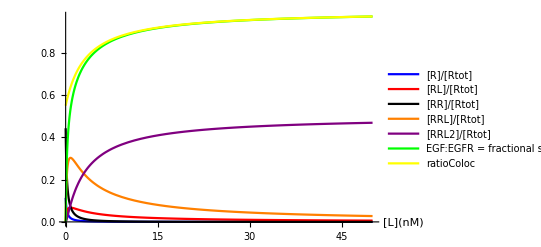
The plot for the original values from the paper [1] was: 
plotModel2Linear[4.6,5.3,0.34,3.9]
-Graphics-

The new plot dividing all equilibrium constants by 10:

In linear scale:

```mathematica
plotModel2Linear[4.6/10,5.3/10,0.34/10,0.26]
```

In log scale:

```mathematica
plotModel2Log[4.6/10,5.3/10,0.34/10,0.26]
```

The new plot dividing all equilibrium constants by 100:

```mathematica
plotModel2Linear[4.6/100,5.3/100,0.34/100,0.037]
```

```mathematica
plotModel2Log[4.6/100,5.3/100,0.34/100,0.037]
```

```mathematica
Manipulate[plotModel2Linear[K11inversenM/multiplier,K21inversenM/multiplier,K22inversenM/multiplier,Afactor],{{K11inversenM,4.6,"K11inversenM"},0,10,0.1},{{K21inversenM,5.3,"K21inversenM"},0,10,0.1},{{K22inversenM,0.34,"K22inversenM"},0,10,0.1},{{Afactor,2,"Afactor"},0,5,0.05},{{multiplier,30,"Dividing Factor"},1,500,1}]
```

Function to extract the value of the fractional saturation, Y, at a given ligand concentration LnM:

```mathematica
ExtractY[K11inversenM_,K21inversenM_,K22inversenM_,Afactor_,LnM_,DividingFactor_]:=(RLr+RRLr+2 RRL2r)/.solModel2/.{K11->K11inversenM/DividingFactor 10^9,K21->K21inversenM/DividingFactor 10^9,K22->K22inversenM/DividingFactor 10^9,A->Afactor,L->LnM 10^-9}
```

Function to extract the value of ratioColoc at a given ligand concentration LnM:

```mathematica
ExtractRatioColoc[K11inversenM_,K21inversenM_,K22inversenM_,Afactor_,LnM_,DividingFactor_]:=((RLr+RRLr+2 RRL2r)/(RLr+2 RRLr+2 RRL2r))/.solModel2/.{K11->K11inversenM/DividingFactor 10^9,K21->K21inversenM/DividingFactor 10^9,K22->K22inversenM/DividingFactor 10^9,A->Afactor,L->LnM 10^-9}
```

Use the following table (from above):
Dividing factor for 
equil assoc constants | Afactor 
= L20 R | L20 
(receptors/cell)^-1 | no. receptors 
per cell | % EGFR in 
monomers | % in dimers
1 | 1.2 | 1/50,000 | 200,000 | 30 | 70
10 | 0.26 | 1/(10 50000) | 200,000 | 66 | 34
30 | 0.11 | 1/(30 50000) | 200,000 | 82 | 18
50 | 0.07 | 1/(50 50000) | 200,000 | 88 | 12
100 | 0.037 | 1/(100 50000) | 200,000 | 93 | 7
1/10 | 4.2 | 10/50,000 | 200,000 | 11 | 89
1/30 | 7.5 | 30/50,000 | 200,000 | 6 | 94
1/50 | 9.8 | 50/50,000 | 200,000 | 5 | 95
1/100 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5

Calculated fractional saturation (Y) values:

```mathematica
resultsYA = ExtractY[4.6,5.3,0.34,1.2,15.6,1]
```

```mathematica
resultsYF = ExtractY[4.6,5.3,0.34,0.26,15.6,10]
```

```mathematica
resultsYG = ExtractY[4.6,5.3,0.34,0.11,15.6,30]
```

```mathematica
resultsYH = ExtractY[4.6,5.3,0.34,0.07,15.6,50]
```

```mathematica
resultsYI= ExtractY[4.6,5.3,0.34,0.037,15.6,100]
```

```mathematica
resultsYB= ExtractY[4.6,5.3,0.34,4.2,15.6,0.1]
```

```mathematica
1/#&/@{0.92,0.76,0.65,0.56,0.405,0.9907}
```

Calculated ratioColoc values:

```mathematica
resultsRatioColocA = ExtractRatioColoc[4.6,5.3,0.34,1.2,15.6,1]
```

```mathematica
resultsRatioColocF = ExtractRatioColoc[4.6,5.3,0.34,0.26,15.6,10]
```

```mathematica
resultsRatioColocG = ExtractRatioColoc[4.6,5.3,0.34,0.11,15.6,30]
```

```mathematica
resultsRatioColocH = ExtractRatioColoc[4.6,5.3,0.34,0.07,15.6,50]
```

```mathematica
resultsRatioColocI= ExtractRatioColoc[4.6,5.3,0.34,0.037,15.6,100]
```

```mathematica
resultsRatioColocB= ExtractRatioColoc[4.6,5.3,0.34,4.2,15.6,0.1]
```

Results:
For all cases, the total number of receptors per cell used is 200,000 receptors/cell.
For all cases, the fractional saturation is evaluated at the ligand concentration in our experiments, ~15.6nM.

Results 1:
All equilibrium association constants, K11, K21 and K22 and L20 are divided by the same factor, “Dividing Factor”, between 10 and 100, to account for the change in temperature corresponding to the constants in the paper. 

Dividing factor for all 
equil assoc constants | Afactor 
= L20 R | L20 
(receptors/cell)^-1 | no. receptors 
per cell | % EGFR in 
monomers | % in dimers | fractional saturation Y
EGF:EGFR in whole cell | 1/Y | ratioColoc
1 | 1.2 | 1/50,000 | 200,000 | 30 | 70 | 0.923 | 1.1 | 0.925
10 | 0.26 | 1/(10 50000) | 200,000 | 66 | 34 | 0.76 | 1.3 | 0.84
30 | 0.11 | 1/(30 50000) | 200,000 | 82 | 18 | 0.65 | 1.5 | 0.90
50 | 0.07 | 1/(50 50000) | 200,000 | 88 | 12 | 0.56 | 1.8 | 0.93
100 | 0.037 | 1/(100 50000) | 200,000 | 93 | 7 | 0.405 | 2.5 | 0.96
1/10 | 4.2 | 10/50,000 | 200,000 | 11 | 89 | 0.991 | 1.01 | 0.991
1/30 | 7.5 | 30/50,000 | 200,000 | 6 | 94 | □ | □ | □
1/50 | 9.8 | 50/50,000 | 200,000 | 5 | 95 | □ | □ | □
1/100 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5 | □ | □ | □

End of the table again so that appears in printing:
fractional saturation Y
EGF:EGFR in whole cell | 1/Y | ratioColoc
0.923 | 1.1 | 0.925
0.76 | 1.3 | 0.84
0.65 | 1.5 | 0.90
0.56 | 1.8 | 0.93
0.405 | 2.5 | 0.96
0.991 | 1.01 | 0.991
□ | □ | □
□ | □ | □
□ | □ | □

For the two extreme cases of the range of dividing factors (10 to 100) that we considered possible for a change of temperature between 37degC and 4degC, we get a fractional saturation Y (EGF:EGFR ratio) of 0.76 and 0.40 (respectively for the dividing factors of 10 and 100). This corresponds to EGFR:EGF ratios of ~1.3 and ~2.5, respectively. So we could say that for our temperature of 37degC, the models predict an EGFR:EGF ratio in the range 1.3 to 2.5 considering dividing factors (to account for temperature difference with respect to equilibrium association constants, K11, K21, K22 measured at 4degC). 
The values we measure (mean values) EGFR:EGF~ 4. 
Additionally, one would have to consider the presence of endocytosis and recycling (not included in the model), that would make the EGFR:EGF ratio larger than that. 
Finally, we would have to consider the fact that in the paper we are only looking at receptor clusters that colocalise with ligand, so the numbers we measure and not exactly the same as the fractional saturation, but they correspond instead to the variable ratioColoc.

Assuming that the value of L20 does not have to change by the same factor as the other association constants (due to temperature), we could do:

```mathematica
ExtractY[4.6,5.3,0.34,13.9,15.6,#]&/@{1,10,30,50,100}
```

```mathematica
ExtractY[4.6,5.3,0.34,4.2,15.6,#]&/@{1,10,30,50,100}
```

```mathematica
ExtractY[4.6,5.3,0.34,1.2,15.6,#]&/@{1,10,30,50,100}
```

```mathematica
ExtractY[4.6,5.3,0.34,0.26,15.6,#]&/@{1,10,30,50,100}
```

```mathematica
ExtractY[4.6,5.3,0.34,0.037,15.6,#]&/@{1,10,30,50,100}
```

So the Y value changes significantly with the Dividing factor for all Afactor values. At higher Dividing factor, the difference for different Afactor values is larger.

Now, keeping instead a constant Dividing factor and changing the A factor, the change is not too drastic over the entire range of Afactor values, i.e. change in L20:

```mathematica
ExtractY[4.6,5.3,0.34,#,15.6,10]&/@{9.8,7.5,4.2,1.2,0.26,0.11,0.07,0.037}
```

```mathematica
ExtractY[4.6,5.3,0.34,#,15.6,30]&/@{9.8,7.5,4.2,1.2,0.26,0.11,0.07,0.037}
```

```mathematica
ExtractY[4.6,5.3,0.34,#,15.6,100]&/@{9.8,7.5,4.2,1.2,0.26,0.11,0.07,0.037}
```

So the value obtained for the fractional saturation at our experimental ligand concentration seems less strongly affected by the chosen value of L20 (equilibrium dimerisation constant, Afactor) and more strongly affected by the change in equilibrium association constants, K11, K21, K22 (due to change in temperature), i.e. by the Dividing Factor.

Choosing an Afactor (and L20) that result in mostly dimers on the cell surface:

It seems reasonable, given that in our experiments we mostly don’t see any monomers, to choose a value of L20 that for a number of receptors of 200,000 per cell results in mostly dimers. This means choosing a high enough Afactor of 1.2 and above even if this means that the equilibrium dimerisation constant L20 is not decreased (due to temperature) by the same factor as all the other equilibrium association constants.

Results 2: 
The equilibrium association constants K11, K21 and K22 are divided by the same factor, “Dividing Factor”, between 10 and 100, to account for the change in temperature. But the dimerisation constant L20 is chosen independently, not divided by the same factor, to ensure that receptors are mostly dimers at the cell surface:

```mathematica
Y1=ExtractY[4.6,5.3,0.34,1.2,15.6,#]&/@{10,30,50,100}
```

```mathematica
Y2=ExtractY[4.6,5.3,0.34,4.2,15.6,#]&/@{10,30,50,100}
```

```mathematica
Y3=ExtractY[4.6,5.3,0.34,13.9,15.6,#]&/@{10,30,50,100}
```

Not much variation in Y across the different Afactor values (vertically in the above).

```mathematica
ExtractRatioColoc[4.6,5.3,0.34,1.2,15.6,#]&/@{10,30,50,100}
```

```mathematica
ExtractRatioColoc[4.6,5.3,0.34,4.2,15.6,#]&/@{10,30,50,100}
```

```mathematica
ExtractRatioColoc[4.6,5.3,0.34,13.9,15.6,#]&/@{10,30,50,100}
```

```mathematica
1/Y1
```

```mathematica
1/Y2
```

```mathematica
1/Y3
```

Results 2 (main results): 

Dividing factor 
for K11,K21, K22 | Afactor 
= L20 R | L20 
(receptors/cell)^-1 | no. receptors 
per cell | % EGFR in 
monomers | % in dimers | fractional saturation Y
EGF:EGFR in whole cell | 1/Y | ratioColoc
10 | 1.2 | 1/50,000 | 200,000 | 30 | 70 | 0.68 | 1.5 | 0.74
30 | 1.2 | 1/50,000 | 200,000 | 30 | 70 | 0.51 | 2.0 | 0.68
50 | 1.2 | 1/50,000 | 200,000 | 30 | 70 | 0.42 | 2.4 | 0.66
100 | 1.2 | 1/50,000 | 200,000 | 30 | 70 | 0.29 | 3.4 | 0.65
10 | 4.2 | 10/50,000 | 200,000 | 11 | 89 | 0.64 | 1.6 | 0.69
30 | 4.2 | 10/50,000 | 200,000 | 11 | 89 | 0.46 | 2.2 | 0.61
0.50 | 4.2 | 10/50,000 | 200,000 | 11 | 89 | 0.38 | 2.7 | 0.59
100 | 4.2 | 10/50,000 | 200,000 | 11 | 89 | 0.26 | 3.8 | 0.57
10 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5 | 0.63 | 1.6 | 0.68
30 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5 | 0.45 | 2.2 | 0.59
50 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5 | 0.36 | 2.8 | 0.56
100 | 13.9 | 100/50,000 | 200,000 | 3.5 | 96.5 | 0.25 | 4.0 | 0.54
End of the table again so that appears in printing:
fractional saturation Y
EGF:EGFR in whole cell | 1/Y | ratioColoc
0.68 | 1.5 | 0.74
0.51 | 2.0 | 0.68
0.42 | 2.4 | 0.66
0.29 | 3.4 | 0.65
0.64 | 1.6 | 0.69
0.46 | 2.2 | 0.61
0.38 | 2.7 | 0.59
0.26 | 3.8 | 0.57
0.63 | 1.6 | 0.68
0.45 | 2.2 | 0.59
0.36 | 2.8 | 0.56
0.25 | 4.0 | 0.54

Considering the range of dividing factors from 10 to 100 (possible for temperature change between 37degC and 4degC), we get a fractional saturation Y (EGF:EGFR ratio) in the range 0.25-0.68 (extreme values: first and last rows). This corresponds to EGFR:EGF ratios of 1.5 - 4.0. So we could say that for our temperature of 37degC, the models predict an EGFR:EGF ratio in the range 1.5 to 4.0 considering dividing factors (to account for temperature difference with respect to equilibrium association constants, K11, K21, K22 measured at 4degC).
The values we measure (mean values) EGFR:EGF~ 4.

### Checking the change with the number of receptors per cell ± SE :

For our experimental data, the number of receptors is 200,000 receptors/cell mean value, with a standard deviation of 220,000, for N=20 cells. Hence, the stardard error of the mean is SE~50,000:

```mathematica
SE = 220000/(√20)//N
```

For the most extreme values (first and last rows of the table), we check the effect on Y of changing the number of receptors per cell by ±SE:

Top row:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/50000),Rtot->250000}//N
```

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/50000),Rtot->150000}//N
```

Afactor is 1.35 (instead of 1.2) when increasing number of receptors by SE.
Afactor is 1 (instead of 1.2) when decreasing number of receptors by SE.

```mathematica
ExtractY[4.6,5.3,0.34,1.35,15.6,10]
```

```mathematica
ExtractY[4.6,5.3,0.34,1,15.6,10]
```

The fractional saturation Y hardly changes, it varies between 0.670 and 0.682 at receptor no. 200,000±50,000(SE), compared to previous value of 0.675 at receptor no. = 200,000.

Bottom row:

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/500),Rtot->250000}//N
```

```mathematica
{100 R/Rtot,100  2 RR/Rtot,L20 R}/.solDimerisat⟦2⟧/.{L20->(1/500),Rtot->150000}//N
```

Afactor is 15.56 (instead of 13.9) when increasing number of receptors by SE.
Afactor is 12 (instead of 13.9) when decreasing number of receptors by SE.

```mathematica
ExtractY[4.6,5.3,0.34,15.56,15.6,100]
```

```mathematica
ExtractY[4.6,5.3,0.34,12,15.6,100]
```

The fractional saturation Y hardly changes, it varies between 0.249 and 0.251 at receptor no. 200,000±50,000(SE), compared to previous value of 0.2499 at receptor no. = 200,000. The % of monomers and dimers are also hardly altered.

Conclusion: The change in the fractional saturation Y (or ratioColoc) with a change in the number of receptors per cell by ±SE is completely negligible compared to the uncertainty in the correction factor due to temperature (the range of values obtained for dividing factors 10-100 is 0.25-0.68 for Y).

### Increasing negative cooperativity of binding:

NEGATIVE COOPERATIVE BINDING when K2 < K1/4.
K11=(4.6±0.6)10^9 M^-1≃4.6 nM^-1(unligated dimer affinity kd1 is~220 pM,inverse of K11)
K21=(5.3±0.4)10^9 M^-1≃5.3 nM^-1(unligated dimer affinity kd1 is~190 pM,inverse of K21)
K22=(3.4±1.1)10^8 M^-1≃0.34 nM^-1(singly-ligated dimer affinity kd2 is~3 nM,inverse of K22).

So K11 and K21 are similar (similar binding affinity for EGF binding to receptor monomer and to unligated receptor dimer. 
The affinity K22 for binding to second site in singly - ligated receptor dimer is ~15 times lower than K21. So it is already negatively cooperative.

Calculating the extremes: cases for dividing Factor = 10, and dividing factor = 100 as for Table of Results 2 (as used before to get ranges):

First row:  	L20 = 1/(500 molecs/cell)
  		A ~ 13.9
  		70 % receptors in dimers, 30 % as monomers
  		Dividing Factor = 10 for K11, K21, K22 only.

```mathematica
YchangeCooperA10=ExtractY[4.6,5.3,#,1.2,15.6,10]&/@{0.34/10,0.34/5,0.34/2,0.34}
```

```mathematica
ratioColocChangeCooperA10=ExtractRatioColoc[4.6,5.3,#,1.2,15.6,10]&/@{0.34/10,0.34/5,0.34/2,0.34}
```

```mathematica
tableChangeCoopA10=TableForm[Thread[{{0.34/10,0.34/5,0.34/2,0.34},YchangeCooperA10,1/YchangeCooperA10,ratioColocChangeCooperA10,1/ratioColocChangeCooperA10}],TableHeadings->{None,{"K22(nM^-1)","Fract.Sat.(EGF:EGFR)","1/Fract.Sat.","ratioColoc(EGF:EGFR)","1/ratioColoc"}}]
```

Last row:   	L20 = 1/(500 molecs/cell), a factor of 100 lower than that in paper [1]
  		A ~ 13.9
  		96.5 % receptors in dimers, 3.5 % as monomers
  		Dividing Factor = 100 for K11, K21, K22 only.

```mathematica
YchangeCooperC100=ExtractY[4.6,5.3,#,13.9,15.6,100]&/@{0.34/10,0.34/5,0.34/2,0.34}
```

```mathematica
ratioColocChangeCooperC100=ExtractRatioColoc[4.6,5.3,#,13.9,15.6,100]&/@{0.34/10,0.34/5,0.34/2,0.34}
```

```mathematica
tableChangeCoopA10=TableForm[Thread[{{0.34/10,0.34/5,0.34/2,0.34},YchangeCooperC100,1/YchangeCooperC100,ratioColocChangeCooperC100,1/ratioColocChangeCooperC100}],TableHeadings->{None,{"K22(nM^-1)","Fract.Sat.(EGF:EGFR)","1/Fract.Sat.","ratioColoc(EGF:EGFR)","1/ratioColoc"}}]
```

Conclusion : 
The starting point (bottom row in both tables) is for K22 being ~15 times lower than K21 and hence already negatively cooperative as K22 < K21/4.
The higher the row in the tables, the more negatively cooperative.
Reducing the value of K22 by a further factor between 2 and 10 (to make the system more negatively cooperative), so to make K22 ~30 times lower and ~150 times lower than K21 (or K11), respectively, only increases the EGFR:EGF ratio slightly.  
Looking at fractional saturations (so counting all EGFR molecules, bound and unbound), when K22 ~ K21/150= 0.034, the range of EGFR:EGF ratio (considering the range for the extreme cases corresponding to a dividing Factor of 10 and 100) goes from the range 1.5 - 4.0 (for K22 = 0.34) to 1.7 - 4.3, i.e., 8-13% higher. 
Looking instead at the ratioColoc (so counting only colocalised EGFR molecules, as in our data), the EGFR:EGF ratioColoc goes from the range 1.4 - 1.86 (for K22 = 0.34) to 1.6 - 1.93 for K22 ~ K21/150= 0.034, i.e., 4-14% higher.

So increasing the negative cooperativity from a ratio K21/K22 = 15 to a ratio K21/K22 = 150 only increases the EGFR:EGF ratio by ~10% roughly.

```mathematica
{0.2/1.5,0.3/4.0,0.2/1.4,0.07/1.9}
```

Plotting for the first and last rows of Table Results 2:

```mathematica
plotModel2Linear[4.6/10,5.3/10,0.34/10,1.2]
```

```mathematica
plotModel2Log[4.6/10,5.3/10,0.34/10,1.2]
```

```mathematica
plotModel2Linear[4.6/100,5.3/100,0.34/100,13.9]
```

```mathematica
plotModel2Log[4.6/100,5.3/100,0.34/100,13.9]
```

## Section 3 - Model for receptor-ligand binding considering both receptor dimers and monomers, and including endocytosis and recycling. Time-dependent model.

This model considers that EGF ligand can bind both to receptor monomers and receptor dimers (similarly to section 2). The model also includes endocytosis of ligated EGFR monomers and dimers and recycling back to the surface of endocytosed EGFR.

Notation: 
R: concentration of receptor monomers ([R])
RR: concentration of receptor dimers ([RR])
RL: concentration of ligated receptor monomers ([RL])
L: concentration of unbound/free ligand (in 3D solution)
RRL: concentration of singly-ligated receptor dimers
RRL2: concentration of doubly-ligated receptor dimers
RL^inside: endocytosed RL
RRL^inside: endocytosed RRL
RRL2^inside: endocytosed RRL2

Reactions:
- The following reversible reactions are the same as in section 2:
R + L -> RL;            with on-rate k_(11,on) and off-rate k_(11,off) and macroscopic equilibrium association constant K11 = k_(11,on)/k_(11,off);
RR + L -> RRL;       with on-rate k_(21,on) and off-rate k_(21,off) and macroscopic equilibrium association constant K21 = k_(21,on)/k_(21,off); 
RRL + L -> RRL2;   with on-rate k_(22,on) and off-rate k_(22,off) and macroscopic equilibrium association constant K22 = k_(22,on)/k_(22,off);
R + R -> RR ;          with macroscopic equilibrium dimerisation constant L20 = l_(20,on)/l_(20,off), with on-rate l_(20,on) and off-rate l_(20,off);
RL + R -> RRL ;      with macroscopic equilibrium dimerisation constant L21 = l_(21,on)/l_(21,off), with on-rate l_(21,on) and off-rate l_(21,off);
RL + RL -> RRL2 ;  with macroscopic equilibrium dimerisation constant L22 = l_(22,on)/l_(22,off), with on-rate l_(22,on) and off-rate l_(22,off).

- Additionally, we have the following non-reversible endocytosis and recycling reactions:
RL -> RL^inside -> R
RRL -> RRL^inside -> RR
RRL2 -> RRL2^inside -> RR
For these three reactions, the first arrow (endocytosis) is considered to have a rate kendoc (in %) and the second arrow (recycling back to cell surface) is considered to have a rate krecycle (in %). We consider only endocytosis of ligated receptors and that recycling is always of unligated receptors. This model results in a conversion of ligated to unligated receptors. In practice, some receptors might be recycled ligated, but this is not considered here for simplicity. 
Also for simplicity, we assume the same endocytosis and recycling rates for ligated monomers and dimers (RL, RRL and RRL2), although these might be different in practice.

Units:
k_(11,on), k_(21,on), k_(22,on) are in units of concentration^-1*time^-1, and specifically here M^-1 s^-1. When they appear in the rate equations, they always multiply [L], which is considered constant with time and which is in units M (molar), so kon*[L] has units of s^-1.
All the off-rates k_(11,off), k_(21,off), k_(22,off), l_(20,off), l_(21,off) and l_(22,off) are in s^-1.
All receptor concentrations (monomer, dimer, ligated, unligated, i.e., [R], [RR], [RL],[RRL], [RRL2] and the inside (endocytosed) components) are in units of concentration as copy number per cell. 
The dimerisation on-rates l_(20,on), l_(21,on) and l_(22,on) are in units of (copies/cell)^-1 s^-1. This is because we have better experimental values (from refs [1] and [8]) in units of inverse 2D concentration, which is what makes sense for cell surfaces. This is ok as, all the receptor concentrations in the rate equations are also in units of copies/cell. 
kendoc and krecycle are in s^-1.

Now, the rate equations to solve (time dependence) are:
d[R]/dt=  - k_(11,on)[R][L]+k_(11,off)[RL] + k_recycle[RL^inside] - (l_(20,on)[R])^2+ l_(20,off)[RR] - l_(21,on)[RL][R] + l_(21,off)[RRL];
d[RR]/dt= (l_(20,on)[R])^2- l_(20,off)[RR] - k_(21,on)[RR][L]+k_(21,off)[RRL] + k_recycle[RRL^inside] + k_recycle[RRL2^inside];
d[RL]/dt= k_(11,on)[R][L]-k_(11,off)[RL] - k_endoc[RL] - l_(21,on)[RL][R] + l_(21,off)[RRL] - (l_(22,on)[RL])^2 + l_(22,off)[RRL2];
d[RRL]/dt= k_(21,on)[RR][L]-k_(21,off)[RRL] - k_endoc[RRL] + l_(21,on)[RL][R] - l_(21,off)[RRL] - k_(22,on)[RRL][L] + k_(22,off)[RRL2];
d[RRL2]/dt= k_(22,on)[RRL][L]-k_(22,off)[RRL2] - k_endoc[RRL2] + (l_(22,on)[RL])^2 - l_(22,off)[RRL2];
d[RL^inside]/dt = k_endoc[RL] - k_recycle[RL^inside];
d[RRL^inside]/dt = k_endoc[RRL] - k_recycle[RRL^inside];
d[RRL2^inside]/dt = k_endoc[RRL2] - k_recycle[RRL2^inside];

The initial conditions at time t=0 are:
[R_(total,0)] = [R_0]+2[RR_0] = 200,000 receptors/cell  (total number of receptors)
[R_0] ≈ 0.05 [R_(total,0)]    (5% monomers)
2 [RR_0] ≈ 0.05 [R_(total,0)]    (95% dimers (or clusters), to match our experimental observations)
[L] ≈ [L0] = 15.6nM = const.
All initial concentrations of ligated receptors [RL_0], [RRL_0], [RRL2_0], are zero, i.e., no ligation at the start.
All initial concentrations of endocytosed (inside) ligated receptors ([RL_0^inside], [RRL_0^inside] and [RRL2_0^inside]) are zero at start.
So we have all initial conditions to save the system.

Note: we assume a large pool of ligand EGF in solution, so that we consider the concentration of ligand, [L] approximately constant throughout and equal to the initial concentration [L0]=15.6nM.

Considering all the on/off-rates, endocytosis/recycling rates, the value of [L] and the initial conditions as parameters, we can solve the system of differential equations for R, RL, RR, RRL, RRL2 and the inside components and calculate and plot fractional concentrations and fractional saturation as a function of time.

It is rather difficult to find the correct parameters. Inserting parameters derived from previous known values and adjusted in several logical ways, did not give any reasonable plots.  So we will first look at each individual reaction separately to obtain reasonable parameters for solving later on the entire system of rate equations.

### Test and solve first only the reaction of R ligand binding:

R + L -> RL;

Conversion of rates adapted from those in the PNAS paper [1] did not work here. 

Reference [4] : 
“Kinetics of binding, endocytosis and recycling of EGF receptor mutants”, S. Felder et al, The Journal of Cell Biology, Volume 117, (1992) 203-212. 
This paper shows that EGF binding reaches equilibrium after ~3-4min, depending on the EGF concentration and depending on the cell line. Association measurements taken at 37degC:

-Graphics-

And from reference [3]:
-Graphics-

I have chosen rates that give a time scale of ligand binding similar to that shown in the above, where equilibrium is reached after ~3-6 min. 
One reviewer mentioned that at 37degC, after ~3min, all receptors are bound.

Useful notes: (not sure about this) changing both k11on and k11off by the same factor changes the time of equilibration but does not change the levels reached at equilibrium. To change the levels reached at equilibrium, change the on-rate and off-rate by different factors. The equilibration time increases when the off-rate decreases (the time constant of the exponential is 1/off-rate). 
- Also play with PrecisionGoal and AccuracyGoal, as sometimes the solution is not found correctly if these are not set correctly. 
- The value of R0 can be set to 1 (the value does not affect the shape of the result, as it is a first order reaction), results obtained are fractions with respect to initial number of receptors.

```mathematica
solveRateEqBind[params_,tfinal_]:= Module[{allEqs,sol},
allEqs = {
RL'[t]==k11on R[t] L-k11off RL[t]/.params,
R[0]==R0/.params,
R[t]==R0-RL[t]/.params,
RL[0]==0
};
sol=NDSolve[allEqs,{R,RL},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞]
]
```

Solve for 10 minutes (600 s):

```mathematica
stest=solveRateEqBind[{R0->1,k11on->1 10^6,k11off->0.001,L->15.6 10^-9},600]
```

```mathematica
Plot[{Evaluate[R[t]/.stest],Evaluate[RL[t]/.stest]},{t,0,600},PlotRange->All,AxesLabel->{"t(s)",None},PlotLegends->{"[R]/R0","[RL]/R0"},PlotLabel->"Ligand Binding"]
```

This assumes that nearly all EGFR copies in cell are bound, i.e. that at our high EGF ligand concentrations, all receptors can be bound in equilibrium and we saturate them, which I think is reasonable according to the above plots (ref. 4).

Using now R0=200,000copies/cell, the result is the same in shape as this is a first order rate equation (first order reaction):

```mathematica
stest2=solveRateEqBind[{R0->200000,k11on->1 10^6,k11off->0.001,L->15.6 10^-9},600];
Plot[{Evaluate[R[t]/.stest2],Evaluate[RL[t]/.stest2]},{t,0,600},PlotRange->All,AxesLabel->{"t(s)",None},PlotLegends->{"[R](copies/cell)","[RL](copies/cell)"},PlotLabel->"Ligand Binding"]
```

The rates of ligand binding/unbinding found by trying to match the timing of the binding give a ratio k11on/k11off = K11 = 1 10^9 M^-1, similar to the inverse of the apparent Kd constant in the table below (matches value in table I below).

Typically, kon~(10^6 - 10^7)M^-1 s^-1 and kd =koff/kon ~(10^-8 - 10^-9)M, at room temperature (from notes above, see Dependence on temperature.)

```mathematica
K11test=k11on/k11off/.{k11on->1 10^6,k11off->0.001}
```

But they do not agree exactly with the ones obtained by fitting in reference [4]:

### Test and solve only for receptor dimerisation:

R + R -> RR;

```mathematica
solveRateEqDimerise[params_,tfinal_]:= Module[{allEqs,sol},
allEqs = {
RR'[t]==l20on (R[t])^2-l20off RR[t]/.params,
R[0]==R0/.params,
R[t]==R0-RR[t]/.params,
RR[0]==0
};
sol=NDSolve[allEqs,{R,RR},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞]
]
```

Note that when we solve this or the equation below, the concentrations [R] and [RR] are given as numbers of individual receptors per cell, i.e., if I have [R0]=200,000 receptors/cell at the start (all monomers and no dimers), and at the end all receptors have dimerised, what I get at the end is [RR]=200,000, which is the copy number of receptors in dimers, not the number of dimers, which would be 1/2 that.
[To get number of dimers, we would have to use in the rate equation that the reaction rate ν=-1/2 d[R]/dt= (kl2on [R])^2, so include that factor of 2. ]

Given the above, the total concentration of ligand-bound receptors (in individual receptor copies/cell) is: 
[Rbound] = [RL] + [RRL]/2 + [RRL2] 	

and the total concentration of unbound receptors (in individual receptor copies/cell) is:
[Runbound] = [R] + [RRL]/2 + [RR]			

The total concentration of receptors is:
[Rtot] = [Rbound] + [Runbound] = [R] + [RL] + [RR] + [RRL] + [RRL2].

The fractional saturation (Y), or, equivalently, the EGF:EGFR ratio, is the ratio of bound receptors to total receptors:

Y =[Rbound]/([Rbound] + [Runbound])= [Rbound]/[Rtot] = [RL]/[Rtot] + [RRL]/[Rtot] + 2[RRL2]/[Rtot]

Note that the following function is equivalent:
(*solveRateEqDimerise[params_,tfinal_]:= Module[{allEqs,sol},
allEqs = {
RR'[t]==l20on (R[t])^2-l20off RR[t]/.params,
R'[t]==-l20on (R[t])^2+l20off RR[t]/.params,
R[0]==R0/.params,
RR[0]==0
};
sol=NDSolve[allEqs,{R,RR},{t,0,tfinal},PrecisionGoal→6,AccuracyGoal→6,MaxSteps→∞]
]*)

In the solution of this, the absolute value of R0 does matter as it is a second order reaction! Use R0=200,000 receptors/cell.

Considering that in our experiments we have mostly dimers or clusters (~95 %) and hardly any monomers (5 %), and assuming a rather fast equilibration of dimerisation with a time constant ~300ms (100ms for GPCreceptors in a Kusumi paper, see reference [8] below), we can choose the following parameters:
- R0 = 200,000 molecules/cell
- l20on=1 10^-4(molecules/cell)^-1 s^-1
-  l20off = 0.1 s^-1.
This leads to L20 = l20on/l20off = 10^-3(copies/cell)^-1. (this is not far from the value in [8], which would be 1/ 2D-KD = 10^-4 (copies/cell)^-1.
These parameters are robust enough, i.e., it does not seem possible to obtain the right equilibration time and right equilibrium levels with other parameters, so they are suitably unique.
It is not possible to obtain equilibrium levels of ~95 % dimers and ~5 % monomers (for our experiments) unless the ratio L20test=l20on/l20offis of the order of 10^-3. This L20 equilibrium association constant is not close to the one in ref [1] (at 4degC, L20 = 1/(50000molecs/cell)=2 10^-5(molecs/cell)^-1), and closer to the one for G-protein coupled receptors in Kusumi’s paper (see ref. [8] below, L20 = 10^-4(molecs/cell)^-1). Interestingly, “our” value L20~10^-3(molecs/cell)^-1, or Kusumi’s value (~10)^-4 [8], both at 37°C are actually larger than that in [1] which was obtained by fitting results at 4°C.

```mathematica
stestDimerise=solveRateEqDimerise[{R0->200000,l20on->1 10^-4 ,l20off->0.1},600];
Plot[{Evaluate[R[t]/.stestDimerise]/200000,Evaluate[RR[t]/.stestDimerise]/200000},{t,0,3},PlotRange->All,AxesLabel->{"t(s)",None},PlotLegends->{"[R]/(200,000receptors/cell)","[RR]/(200,000receptors/cell)"},PlotLabel->"Dimerisation"]
```

```mathematica
L20test=l20on/l20off/.{l20on->1 10^-4 ,l20off->0.1}
```

For slower equilibration on a time scale of approx. 60s, use: {R0→200000,l20on→2 10^-6 ,l20off→1000 10^-6}:

```mathematica
stestDimerise2=solveRateEqDimerise[{R0->200000,l20on->10^-6 ,l20off->10^-3},600];
Plot[{Evaluate[R[t]/.stestDimerise2]/200000,Evaluate[RR[t]/.stestDimerise2]/200000},{t,0,100},PlotRange->All,AxesLabel->{"t(s)",None},PlotLegends->{"[R]/(200,000receptors/cell)","[RR]/(200,000receptors/cell)"},PlotLabel->"Dimerisation"]
L20test=l20on/l20off/.{l20on->10^-6 ,l20off->10^-3}//N
```

For an even slower equilibration on a time scale of approx. 10 min =600s, use: {l20on→2 10^-7 ,l20off→1 10^-4}:

```mathematica
stestDimerise2=solveRateEqDimerise[{R0->200000,l20on->10^-7 ,l20off->1 10^-4},600];
Plot[{Evaluate[R[t]/.stestDimerise2]/200000,Evaluate[RR[t]/.stestDimerise2]/200000},{t,0,600},PlotRange->All,AxesLabel->{"t(s)",None},PlotLegends->{"[R]/(200,000receptors/cell)","[RR]/(200,000receptors/cell)"},PlotLabel->"Dimerisation"]
L20test=l20on/l20off/.{l20on->10^-7 ,l20off->1 10^-4}//N
```

Reference 5 : “Effect of Phosphorylation on EGFR Dimer Stability Probed bySingle - Molecule Dynamics and FRET/FLIM”, Oana Coban, ..., Marisa L. Martin-Fernandez, Biophysical J. 108, 1013-1026 (2015). 
See Fig. 2: “the distribution of more than 2000 dimerization events was fitted to a monoexponential where koff = 1.19 +-0.05 s^-1”, but in this paper, the percentage of homodimers on the cells (at equilibrium) was only ~20% (very different to our experiments, so likely different rate).
Not much is known or has been measured about the time dependence of receptor dimerisation. 

Reference 6: “EGFR Ligands Differentially Stabilize ReceptorDimers to Specify Signaling Kinetics”, D.M. Freed et al., Cell 171, 683–695 (2017).
See page 688: EGF (~500 receptors per micron^2) inFigures 5B and 5C corresponds to a local EGFR concentration of ~80mM, or ~200,000 receptors/cell. 

Reference 7: “Epidermal Growth Factor Receptor Dimerization and ActivationRequire Ligand-Induced Conformational Changes in the Dimer Interface”, Jessica P. Dawson et al. MOLECULAR  AND CELLULAR BIOLOGY 25, 7734–7742 (2005). 
Ligand binding dissociation constants (affinity K_D=koff/kon) measured with Biacore SPR (on surface, not on cells) at 25degC is K_D~200 nM, which means that its inverse, K_A~K11=5 x10^-3 nM^-1. This is 3 orders of magnitude lower than the K11 value in reference [1] (see below). Some of that factor might be due to temperature, as values in [1] where for 4degC, and also to the fact that it’s on Biacore.
For receptor dimerisation, K_D :

-Graphics-
Reference 8: “Full characterization of GPCR monomer–dimer dynamic equilibrium by single molecule imaging”, Rinshi S. Kasai,..., A. Kusumi. J Cell Biol. 2011 Feb 7; 192(3): 463–480. doi: 10.1083/jcb.201009128:
Abstract: Receptor dimerization is important for many signaling pathways. However, the monomer–dimer equilibrium has never been fully characterized for any receptor with a 2D equilibrium constant as well as association/dissociation rate constants (termed super-quantification). Here, we determined the dynamic equilibrium for the N-formyl peptide receptor (FPR), a chemoattractant G protein–coupled receptor (GPCR), in live cells at 37°C by developing a single fluorescent-molecule imaging method. Both before and after liganding, the dimer–monomer 2D equilibrium is unchanged, giving an equilibrium constant (this is affinity K_D) of 3.6 copies/µm^2, with a dissociation and 2D association rate constant of 11.0 s^−1 and 3.1 (copies/µm^2)^-1*s^−1, respectively. At physiological expression levels of ∼2.1 receptor copies/µm^2 (∼6,000 copies/cell), monomers continually convert into dimers every 150 ms, dimers dissociate into monomers in 91 ms, and at any moment, 2,500 and 3,500 receptor molecules participate in transient dimers and monomers, respectively. Not only do FPR dimers fall apart rapidly, but FPR monomers also convert into dimers very quickly.

-Graphics--Graphics-
-Graphics-

So: 2.1receptor copies/micron^2 corresponds to 6000 copies/cell, approx. Hence, 1receptor copies/micron^2 = 2857 copies/cell.
The association constant ka for dimerisation is hence: ka = 3.1/2857 (copies/cell)^-1 s^-1= 1.1×10^-3 (copies/cell)^-1 s^-1. (This would be l20on.) 
(And l2off would be kd~10 s^-1.)
The 2D-KD = 3.6 copies/micron^2 = 3.6*2857 ≈10^4copies/cell.
This is all for a GPCR, not for EGFR, but we can assume that it’s similar diffusion, etc for EGFR.
So the rate of conversion is quick, with a lifetime of ~100ms. 

From reference [1] [PNAS 105, 112-117 (2008)] from measurements in CHO cells at 4 degC: 
K11 =  (4.6±0.6) 10^9 M^-1≃ 4.6 nM^-1  (unligated dimer affinity kd1 is ~220 pM, inverse of K11)
K21 = (5.3±0.4) 10^9 M^-1≃ 5.3 nM^-1  (unligated dimer affinity kd1 is ~190 pM, inverse of K21)
K22 = (3.4±1.1) 10^8 M^-1≃ 0.34 nM^-1 (singly-ligated dimer affinity kd2 is ~3 nM, inverse of K22).
L20 = (5.3±2.2) 10^11(mol/dm^2)^-1 in units of 2D surface concentration. This corresponds to ~50,000 receptors per cell, so L20 = (50,000 molecs/cell)^-1= 2*10^-5(molecs/cell)^-1.

```mathematica
6000/2.1{0.3,2.5}
```

```mathematica
3.1/2857
```

```mathematica
3.6*2857
```

```mathematica
1/50000//N
```

### Notes on endocytosis and recycling rates :

From email from Alexander Sorkin to M. Leake, we know that endocytosis rate is typically 4-10%/min for high EGF concentrations ([EGF]~100ng/ml, like the ones in our experiments), where likely we saturate all EGFRs at the cell surface and the clathrin endocytosis pathway is saturated. At low [EGF] (physiological [EGF]~1ng/ml), the typical rates are 15-30%/min. 
In same email, A. S. says that recycling rates of ligand-occupied receptors are ~10%/min and that recycling contributes significantly only after ~5min of initial endocytosis, when a significant pool of endosomal EGFR is accumulated.
At [EGF]~100ng/ml, in HeLa cells, more than 50% of EGFR are transferred from plasma membrane to endosomes in 30 min. 

References [2] and [3] (details above) also give endocytosis rates for EGFR of 10-30%/min. 

Also, reference [9]: “Clathrin-mediated internalization is essential for sustained EGFR signalling but dispensable for degradation”, Developmental Cell 15, 209 (2008) is nice and clear. There are two pathways for EGFR internalization: clathrin-mediated endocytosis (CME), which mostly leads to recycling of receptors to the cell surface; and non-clathrin endocytosis (clathrin independent internalization) (NCE), which mostly leads to receptor degradation. At low doses of EGF, mostly we have CME. At high EGF doses, we have mixture of CME+NCE. The high EGF concentration they use is [EGF]=100ng/ml, so the dose in our experiments. 
At low [EGF]~1.5ng/ml (~physiological): kendoc=0.33/min (33%/min).
At high [EGF]~100ng/ml (~physiological): kendoc=0.17/min (17%/min).
This is more or less consistent with the info form A. Sorkin’s email.
The CME pathway results in ~60-65% being recycled and ~30% being degraded.
The NCE pathway results in 80-90% being degraded and ~10-20% being recycled.
At high [EGF], ~60% goes through CME pathway and ~40% through NCE pathway, resulting in a total of ~40% being recycled and ~55% being degraded.
I believe these are long-term equilibrium values, not rates. 

From the sections below, it looks like the recycling rate makes only a very small difference in the modelled surface fractional saturation, Y.

Note that the model effectively has no receptor degradation.This could be included but since our receptor numbers don’t seem to change with time, I thought we might leave it out.

In the calculations below, I use values from 4%/min to 30%/min for the endocytosis rates, and mostly 10%/min; and 10%/min for the recycling rates.

### Solving all rate equations together:

The system of differential equations is :

```mathematica
diffEqs[params_]:={
(*R'[t]==-k11on R[t] L+k11off RL[t]+krecycle RLinside[t]-l20on (R[t])^2+l20off RR[t]-l21on RL[t] R[t]+l21off RRL[t],*)
RR'[t]==l20on (R[t])^2-l20off RR[t]-k21on RR[t] L+k21off RRL[t]+krecycle RRLinside[t]+krecycle RRL2inside[t],
RL'[t]==k11on R[t] L-k11off RL[t]-kendoc RL[t]-l21on RL[t] R[t]+l21off RRL[t]-l22on (RL[t])^2+l22off RRL2[t],
RRL'[t]==k21on RR[t] L-k21off RRL[t]-kendoc RRL[t]+l21on RL[t] R[t]-l21off RRL[t]-k22on RRL[t] L+k22off RRL2[t],
RRL2'[t]==k22on RRL[t] L-k22off RRL2[t]-kendoc RRL2[t]+l22on (RL[t])^2-l22off RRL2[t],
RLinside'[t]==kendoc RL[t]-krecycle RLinside[t],
RRLinside'[t]==kendoc RRL[t]-krecycle RRLinside[t],
RRL2inside'[t]==kendoc RRL2[t]-krecycle RRL2inside[t],
R[t]==totalNoReceptors-(RR[t]+RL[t]+RRL[t]+RRL2[t]+RLinside[t]+RRLinside[t]+RRL2inside[t])
}/.params;
```

Important note: the last equation (instead of the rate equation for R’[t]) is necessary to guarantee that the total number of receptors is never larger than the parameter totalNoReceptors (total number of molecule copies of R in the cell). Used for the first reactant in the chain.
In order to include degradation of receptors, we could include a variable Rdegraded which comes from degrading endocytosed receptors, so that what is not recycled is degraded, by then including in the RHS of the last equation also Rdegraded. This would lead to loss of receptors from the cell surface.

The input list “params” contains all the parameters: the on/off rates, kendoc, krecycle, L, totalNoReceptors, monomerFraction0 and dimerFraction0, with:
  - totalNoReceptors = total number of receptors in the cell; for EGFR in our experiments this is 200,000 molecs/cell;
  - monomerFraction0 = initial fraction of monomers on cell surface, e.g. monomerFraction0 = 0.3 for 30% monomers;
  - dimerFraction0 = initial fraction of dimers on cell surface, e.g. dimerFraction0 = 0.7 for 70% dimers.

The initial conditions (at t=0) are the following (all in units of receptors/cell):

```mathematica
initialConds[params_]:= {
R[0]==monomerFraction0 totalNoReceptors/.params,
RR[0]==dimerFraction0 totalNoReceptors/.params (*we count number of molecules (individual receptor molecules), not number of dimers*),
RL[0]==0,
RRL[0]==0,
RRL2[0]==0,
RLinside[0]==0,
RRLinside[0]==0,
RRL2inside[0]==0
};
```

Solve the system of differential equations:

```mathematica
solveRateEqsModel3[params_,tfinal_]:= Module[{allEqs,sol},
allEqs = Join[diffEqs[params],initialConds[params]];
sol=NDSolve[allEqs,{R,RR,RL,RRL,RRL2,RLinside,RRLinside,RRL2inside},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞]
]
```

```mathematica
(*,PrecisionGoal->6,AccuracyGoal->6,Method->{ExplicitRungeKutta,"StiffnessTest"->False,"DifferenceOrder"->5},MaxSteps->∞]*)
```

```mathematica
params0={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
```

```mathematica
s=solveRateEqsModel3[params0,2400];
```

```mathematica
Plot[{Evaluate[R[60 min]/.s],Evaluate[RR[60 min]/.s],Evaluate[RL[60 min]/.s],Evaluate[RRL[60 min]/.s],Evaluate[RRL2[60 min]/.s],Evaluate[RLinside[60 min]/.s],Evaluate[RRLinside[60 min]/.s],Evaluate[RRL2inside[60 min]/.s]},{min,0,40},PlotRange->All,AxesLabel->{"t(min)",None},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Dashed,Dashed,Dashed},PlotLegends->{"[R](molecs/cell)","[RR](molecs/cell)","[RL](molecs/cell)","[RRL](molecs/cell)","[RRL2](molecs/cell)","[RLinside](molecs/cell)","[RRLinside](molecs/cell)","[RRL2inside](molecs/cell)"}]
```

Note that when we solve the rate equations , the concentrations [R], [RR], etc. are given as numbers of individual receptors per cell, i.e., if I have [R0]=200,000 receptors/cell at the start (all monomers and no dimers), and at the end all receptors have dimerised, what I get at the end is [RR]=200,000, which is the copy number of receptors in dimers, not the number of dimers, which would be 1/2 that.

Given the above, the total concentration of ligand-bound receptors (in individual receptor copies/cell) is: 
[Rbound]^surface = [RL] + [RRL]/2 + [RRL2] 	

and the total concentration of unbound receptors (in individual receptor copies/cell) is:
[Runbound]^surface = [R] + [RRL]/2 + [RR]			

The total concentration of receptors everywhere is:
[Rtot] = [Rbound] + [Runbound] = [R] + [RL] + [RR] + [RRL] + [RRL2]+[RLinside]+[RRLinside]+[RRL2inside].

The fractional saturation (Y) measured on the cell surface, or, equivalently, the EGF:EGFR ratio, is the ratio of bound receptors to total receptors on the surface:

Y =[Rbound]^surface/([Rbound]^surface + [Runbound]^surface)= ([RL] + [RRL]/2 + [RRL2])/([R] + [RL]+[RR]+[RRL]+[RRL2])

```mathematica
Plot[{Evaluate[((RL[60 min]+RRL[60 min]/2+RRL2[60 min])/(R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]))/.s],Evaluate[((R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]+RLinside[60 min]+RRLinside[60 min]+RRL2inside[60 min])/(totalNoReceptors/.params0))]/.s},{min,0,40},PlotRange->All,AxesLabel->{"t(min)",None},PlotLegends->{"Y, fractional saturation on cell surface, EGF:EGFR",StringTemplate["[Rtotal]/(`1` molecs/cell)"][NumberForm[totalNoReceptors/.params0,2]]}]
```

#### Define new function to solve and plot in one go (first output is solution, second and third outputs are the plots above):

```mathematica
solveAndPlotRateEqsModel3[params_,tfinal_]:= Module[{allEqs,sol,plot1,plot2,totalRonSurfaceFinal,Yfinal},
allEqs = Join[diffEqs[params],initialConds[params]];
sol=NDSolve[allEqs,{R,RR,RL,RRL,RRL2,RLinside,RRLinside,RRL2inside},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞];
plot1=Plot[{Evaluate[R[60 min]/.sol],Evaluate[RR[60 min]/.sol],Evaluate[RL[60 min]/.sol],Evaluate[RRL[60 min]/.sol],Evaluate[RRL2[60 min]/.sol],Evaluate[RLinside[60 min]/.sol],Evaluate[RRLinside[60 min]/.sol],Evaluate[RRL2inside[60 min]/.sol]},{min,0,40},PlotRange->All,AxesLabel->{"t(min)",None},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Dashed,Dashed,Dashed},PlotLegends->{"[R] (molecs/cell)","[RR] (molecs/cell)","[RL] (molecs/cell)","[RRL] (molecs/cell)","[RRL2] (molecs/cell)","[RLinside] (molecs/cell)","[RRLinside] (molecs/cell)","[RRL2inside] (molecs/cell)"}];
plot2=Plot[{Evaluate[((RL[60 min]+RRL[60 min]/2+RRL2[60 min])/(R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]))/.sol],Evaluate[((R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]+RLinside[60 min]+RRLinside[60 min]+RRL2inside[60 min])/(totalNoReceptors/.params))]/.sol,
Evaluate[((R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min])/(totalNoReceptors/.params))]/.sol
},{min,0,40},PlotRange->All,AxesLabel->{"t(min)",None},PlotLegends->{"Y, fractional saturation on cell surface, EGF:EGFR",StringTemplate["[Rtotal]/(`1` molecs/cell)"][NumberForm[totalNoReceptors/.params,2]],
StringTemplate["Total no. of R molecs on surface/(`1` molecs/cell)"][NumberForm[totalNoReceptors/.params,2]]
}];
totalRonSurfaceFinal =Evaluate[(R[tfinal]+RL[tfinal]+RR[tfinal]+RRL[tfinal]+RRL2[tfinal])]/.sol;
Yfinal =Evaluate[((RL[tfinal]+RRL[tfinal]/2+RRL2[tfinal])/(R[tfinal]+RL[tfinal]+RR[tfinal]+RRL[tfinal]+RRL2[tfinal]))/.sol];
{sol,
plot1,
plot2,
StringTemplate["Total no. of R molecs on cell surface at final time is: `1` "][NumberForm[totalRonSurfaceFinal⟦1⟧,2]],
StringTemplate["Surface fractional saturation Y at final time is: `1` "][NumberForm[Yfinal⟦1⟧ ,2]]
}
]
```

```mathematica
solf=solveAndPlotRateEqsModel3[params0,2400];
solf⟦2⟧
solf⟦3⟧
solf⟦4⟧
solf⟦5⟧
```

Note that the above reproduces the correct time scale of endocytosis (see plots from ref. [3]), i.e., the internalised receptors reach equilibrium (saturate) after ~30-40 min.
So params0 works quite well:
params0={
totalNoReceptors→310000(*molecules/cell*),
monomerFraction0→0.05,
dimerFraction0→0.95,
L→15.6 10^-9 (*units are M*),
k11on→10^6(*units are M^-1 s^-1, 10^7 default*),
k11off→10^-3(*units are M^-1 s^-1*),
k21on→10^6(*units are M^-1 s^-1*),
k21off→10^-3(*units are s^-1*),
k22on→10^6/7(*units are M^-1 s^-1*),
k22off→2 10^-3(*units are s^-1*),
l20on→10^-4(*units are 1/(molecules/cell)s^-1*),
l20off→0.1(*units are s^-1*),
l21on→10^-4(*units are 1/(molecules/cell)s^-1*),
l21off→0.1(*units are s^-1*),
l22on→10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off→2 0.1(*units are s^-1*),
kendoc→0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle→0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);

#### Without ligand binding (with dimerisation, endocytosis and recycling):

```mathematica
params1={
totalNoReceptors->200000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->0 10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->0 10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->0 10^6/7(*units are s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.1/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol1=solveAndPlotRateEqsModel3[params1,2400];
sol1⟦2⟧
sol1⟦3⟧
sol1⟦4⟧
sol1⟦5⟧
```

```mathematica
Plot[{Evaluate[R[t]/.sol1⟦1⟧],Evaluate[RR[t]/.sol1⟦1⟧],Evaluate[RL[t]/.sol1⟦1⟧],Evaluate[RRL[t]/.sol1⟦1⟧],Evaluate[RRL2[t]/.sol1⟦1⟧],Evaluate[RLinside[t]/.sol1⟦1⟧],Evaluate[RRLinside[t]/.sol1⟦1⟧],Evaluate[RRL2inside[t]/.sol1⟦1⟧]},{t,0,3},PlotRange->All,AxesLabel->{"t(s)",None},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Dashed,Dashed,Dashed},PlotLegends->{"[R](molecs/cell)","[RR](molecs/cell)","[RL](molecs/cell)","[RRL](molecs/cell)","[RRL2](molecs/cell)","[RLinside](molecs/cell)","[RRLinside](molecs/cell)","[RRL2inside](molecs/cell)"}]
```

Without ligand binding, nothing happens, only the short time (~1s) equilibration of receptor dimerisation (R+R->RR). As there is no ligation and in our model only ligated receptors are endocytosed, there is no endocytosis.

#### Ligand binding only to monomers (no ligand binding to dimers) with dimerisation, endocytosis and recycling:

```mathematica
params2={
totalNoReceptors->250000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->0 10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->0 10^6/7(*units are s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol2=solveAndPlotRateEqsModel3[params2,2400];
sol2⟦2⟧
sol2⟦3⟧
sol2⟦4⟧
sol2⟦5⟧
```

In this case, the expected Y is ~0.24 (corresponding to EGFR:EGF ~4). In this case, EGF binds receptor monomers but not dimers. In this case, we would observe at the surface mostly unligated and ligated dimers, RR and RRL, only. And after ~8-10 min, the number of receptors on the cell surface would be ~constant.

Note that the number of receptors on the surface at the end is only ~80% of the total number of receptors used as input (“totalNoReceptors”). Hence, to measure 200,000 on the surface, we need to have totalNoReceptors~250,000 in total at the start:

Using totalNoReceptors -> 250000, changing the rate of endocytosis and the rate of recycling. What changes is in blue:

kendoc(s^-1) | krecycle (s^-1) | Y (t=40min)
0.04/60 | 0.1/60 | 0.27
0.06/60 | 0.1/60 | 0.24
0.1/60 | 0.1/60 | 0.19
0.2/60 | 0.1/60 | 0.13
0.3/60 | 0.1/60 | 0.097
0.06/60 | 0.1/60 | 0.24
0.06/60 | 0.2/60 | 0.23
0.06/60 | 0.4/60 | 0.22
0.06/60 | 0.6/60 | 0.22

#### Rates that exactly match the equilibrium constants (K11, K21, K22, L20, etc.) from reference [1] (measured at 4degC):

These rates predict a Y~0.95 at equilibrium, using totalNoReceptors→310,000, in order to get a total number of R molecules on the surface of ~200,000.
Using totalNoReceptors→200,000, which results in only 130,000 R molecules on the surface at equilibrium, gives a very similar Y~0.96.
So the total no. of receptors does not have a big effect within the same order of magnitude.
This is consistent with Model 2 above (steady state equilibrium model without endocytosis), which predicts a Y very close to 1 at our ligand concentration. 
Changing the values of k22on, k22off from 10^7/14 and 3 10^-3  to 10^7 and 14 3 10^-3 changes the result for Y(tfinal) only by ~3% for the second case and no change for the first case. 
Changing the endocytosis rate (and/or not the recycling rate) to 0.4/60, only changes Y a bit, to Y~0.92.

```mathematica
10^7/(2 10^-3)//N
```

```mathematica
1/50000//N
```

```mathematica
params3={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^7(*units are M^-1 s^-1, 10^7 default*),
k11off->2 10^-3(*units are M^-1 s^-1*),
k21on->10^7(*units are M^-1 s^-1*),
k21off->2 10^-3(*units are s^-1*),
k22on-> 10^7/7(*units are s^-1*),
k22off->2 2 10^-3(*units are s^-1*),
l20on->1/50000(*units are 1/(molecules/cell)s^-1*),
l20off->1(*units are s^-1*),
l21on->1/50000(*units are 1/(molecules/cell)s^-1*),
l21off->1(*units are s^-1*),
l22on->1/(5 50000)(*units are 1/(molecules/cell)s^-1*),
l22off->2 1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol3=solveAndPlotRateEqsModel3[params3,2400];
sol3⟦2⟧
sol3⟦3⟧
sol3⟦4⟧
sol3⟦5⟧
```

When going from 4degC to 37degC, we know that the equilibrium constants, ratio of on/off rates, can change by a factor of up to 100, mostly via increase of off-rate.
Increasing all off-rates by a factor of 100 to account for the increase in temperature does not give meaningful results, as binding equilibrium is reached way too quickly compared to measured binding in experiments (see papers in section above), and the dominant effect is that of endocytosis.

```mathematica
params3={
totalNoReceptors->240000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^7(*units are M^-1 s^-1, 10^7 default*),
k11off->3 10^-1(*units are M^-1 s^-1*),
k21on->10^7(*units are M^-1 s^-1*),
k21off->3 10^-1(*units are s^-1*),
k22on-> 10^7/7(*units are s^-1*),
k22off->1 3 10^-1(*units are s^-1*),
l20on->1.2/50000(*units are 1/(molecules/cell)s^-1*),
l20off->100(*units are s^-1*),
l21on->1.2/50000(*units are 1/(molecules/cell)s^-1*),
l21off->100(*units are s^-1*),
l22on->1.2/(5 50000)(*units are 1/(molecules/cell)s^-1*),
l22off->2 100(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol3=solveAndPlotRateEqsModel3[params3,2400];
sol3⟦2⟧
sol3⟦3⟧
sol3⟦4⟧
sol3⟦5⟧
```

#### Variations around params0:

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

```mathematica
1/0.66
```

```mathematica
100 0.02/0.66
```

RESULTS
Changing totalNoReceptors:
totalNoReceptors = 200,000 -> Yfinal=0.67;    Total no. of R molecs on cell surface at final time is: 130,000;
totalNoReceptors = 310,000 -> Yfinal=0.66;    Total no. of R molecs on cell surface at final time is: 200,000;
totalNoReceptors = 410,000 -> Yfinal=0.66;    Total no. of R molecs on cell surface at final time is: 270,000.

Changing kendoc, using totalNoReceptors = 310,000:
kendoc→0.03/60 s^-1 ->  Yfinal=0.72;    Total R molecs final = 130,000; Internalisation saturates in ~30 min (closer to real experiments).
kendoc→0.06/60 s^-1 ->  Yfinal=0.66;    Total R molecs final = 200,000; Internalisation saturates in ~30 min (closer to real experiments).
kendoc→0.1/60 s^-1 ->   Yfinal=0.62;    Total R molecs final = 170,000; Internalisation saturates in ~28 min (closer to real experiments).
kendoc→0.2/60 s^-1 ->   Yfinal=0.53;    Total R molecs final = 120,000; Internalisation saturates in ~12-14min.
It makes sense to keep kendoc in the range: (0.03/60-0.1/60)s^-1, so stick to 0.06/60s^-1.

Changing krecycle, using totalNoReceptors = 310,000 and kendoc→0.06/60 s^-1:
Changing from krecycle = 0.1/60 s^-1 to krecycle = 0.4/60 s^-1, does not change Y, i.e., Y=0.66. Total R molecs final = 270,000.
Changing krecycle to 0, leads to Y~0.83, no equilibration after 40min and Total R molecs final = 33,000 only.

MORE RESULTS

Changing the time constant of dimerisation via changing dimerisation rates (@ kendoc= 0.06/60 s^-1 and krecycle = 0.1/60 s^-1):
Reducing all dimerization on-rates and off-rates by a factor of 100, which keeps the same L20 = 10^-3 (molec/cell)^-1, but results in an equilibration time for dimerisation of 60s, instead of ~1s for params0, Y ~ 0.68 (instead of Y=0.66). This corresponds to changing from params0 to:

l20on→10^-6(*units are 1/(molecules/cell)s^-1*),
l20off→10^-3(*units are s^-1*),
l21on→10^-6(*units are 1/(molecules/cell)s^-1*),
l21off→10^-3(*units are s^-1*),
l22on→10^-6/5(*units are 1/(molecules/cell)s^-1*),
l22off→2 10^-3(*units are s^-1*)

Reducing all dimerization on-rates and off-rates by a factor of 1000, which keeps the same L20 = 10^-3 (molec/cell)^-1, but results in an equilibration time for dimerisation of 10minutes = 600s, instead of ~1s for params0, the value of Y only very slightly changes from Y=0.66 to Y=0.68 and the Total R molecs final stays the same.  This corresponds to changing from params0 to:

l20on→10^-7(*units are 1/(molecules/cell)s^-1*),
l20off→10^-4(*units are s^-1*),
l21on→10^-7(*units are 1/(molecules/cell)s^-1*),
l21off→10^-4(*units are s^-1*),
l22on→10^-7/5(*units are 1/(molecules/cell)s^-1*),
l22off→2 10^-4(*units are s^-1*)

Results shown below.

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-6(*units are 1/(molecules/cell)s^-1*),
l20off->10^-3(*units are s^-1*),
l21on->10^-6(*units are 1/(molecules/cell)s^-1*),
l21off->10^-3(*units are s^-1*),
l22on->10^-6/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 10^-3(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-7(*units are 1/(molecules/cell)s^-1*),
l20off->10^-4(*units are s^-1*),
l21on->10^-7(*units are 1/(molecules/cell)s^-1*),
l21off->10^-4(*units are s^-1*),
l22on->10^-7/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 10^-4(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

Changing fractions of monomers/dimers at start (and dimerisation rates):

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.90,
dimerFraction0->0.1,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

Changing the fraction of monomers from 5% to 90% (using equilibration rates for dimerisation of 1s up to 600s (10min)) does not really change the value of Y at equilibrium (as the equilibration time of dimerization is short (~1s)).

Changing the concentration of ligand:

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

Using totalNoReceptors→310000 and changing the concentration of ligand:
 For [L] =   10 nM -> Yfinal=0.59;    Total no. of R molecs on cell surface at final time is: 210,000;
 For [L] =15.6 nM -> Yfinal=0.66;    Total no. of R molecs on cell surface at final time is: 200,000;
 For [L] =   20 nM -> Yfinal=0.7;    Total no. of R molecs on cell surface at final time is: 200,000;

 For [L] = 1 nM (physiological) with totalNoReceptors→240000 -> Yfinal=0.19;  Total no. R molecs final = 200,000;

Changing cooperativity:

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

Extreme negative cooperativity:
Leaving k11on and k21on as they are (so both R and RR can bind to ligand) and switching k22on to zero (ligand cannot bind to singly-ligated receptors, only to unligated receptors). Y = 0.66, i.e. no changes. This is the same leaving the rate k22off as it was or switching it to zero: 
 k22on = 10^6/7 M^-1 s^-1, k22off=2 10^-3 s^-1  -> Yfinal=0.66;    Total no. of R molecs on cell surface at final time is: 200,000;
 k22on = 0,                   k22off=2 10^-3 s^-1  -> Yfinal=0.66;    Total no. of R molecs on cell surface at final time is: 200,000;
 k22on = 0,                 k22off=0                  -> Yfinal=0.66;    Total no. of R molecs on cell surface at final time is: 200,000;

No binding to unligated dimers (k21on = 0), setting totalNoReceptors→250000(*molecules/cell*):
k22on = 0 or 10^6/7 M^-1 s^-1; k22off=0 or 2 10^-3 s^-1;   k21on = 0    -> Yfinal=0.24;    Total no. R molecs final = 200,000;
k21on = 0 and k21off = 0, gives Yfinal=0.38;

All rates on as in params0 except for k11on = 0  -> Yfinal=0.63;    Total no. of R molecs on cell surface at final time is: 200,000 using totalNoReceptors→310000.

So setting k21on = 0 (with k220n = 0 or not) makes a large difference, i.e., if ligand can bind to receptor monomers (R) (and to RRL or not) but not to unligated dimers RR. RRL then forms through other processes (see rate eqns).
  
 
Positive cooperativity: k22on = k11on and k22off = k11off: only very slight change:
k22on→10^6/1(*units are M^-1 s^-1*),
k22off→1 10^-3(*units are s^-1*),
-> Yfinal=0.69;    Total no. of R molecs on cell surface at final time is: 200,000;
Even more positive cooperativity: k22on = 10*k11on and k22off = k11off:  results in small change:
k22on→10^7/1(*units are M^-1 s^-1*),
k22off→1 10^-3(*units are s^-1*),
-> Yfinal=0.82;    Total no. of R molecs on cell surface at final time is: 200,000;

So changing the cooperativity, i.e. the ratio of K22on to K11on, does not change Y that much. Even for the case of extreme negative cooperativity (k22on = 0), the Y value does not change. Positive cooperativity leads to higher Y values and negative cooperativity to lower values, so negative cooperativity agrees better with an EGFR:EGF ratio at the cell surface (1/Y) of ~4 on average.

Changing dimerisation rates :

```mathematica
params4={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->0 10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0 0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol4=solveAndPlotRateEqsModel3[params4,2400];
sol4⟦2⟧
sol4⟦3⟧
sol4⟦4⟧
sol4⟦5⟧
```

Setting l20on→0  (R and R do not dimerise to form RR)
-> Yfinal=0.49;    Total no. of R molecs on cell surface at final time is: 200,000;

Setting l20on→0, (R and R do not dimerise to form RR)
l20off→0                   :
-> Yfinal=0.69;    Total no. of R molecs on cell surface at final time is: 200,000;


Setting l21on→0  (RL and R do not dimerise to form RRL):
-> Yfinal=0.92;    Total no. of R molecs on cell surface at final time is: 200,000;

Setting l21on→0  (RL and R do not dimerise)
l21off→0                      :
-> Yfinal=0.69;    Total no. of R molecs on cell surface at final time is: 200,000;


Setting l22on→0  (RL and RL do not dimerise to form RRL2)
-> Yfinal=0.53;    Total no. of R molecs on cell surface at final time is: 200,000;

Setting l22on→0, (RL and RL do not dimerise to form RRL2)
l22off→0                   :
-> Yfinal=0.68;    Total no. of R molecs on cell surface at final time is: 200,000;


Setting l22on→0  (RL and RL do not dimerise to form RRL2) 
              l20on→0  (R and R do not dimerise to form RR):
-> Yfinal=0.47;    Total no. of R molecs on cell surface at final time is: 200,000;

Conclusion : 
So the results for Y at equilibrium don’t change very much upon changing various parameters. 
The parameters that affect the value of Y(t=tfinal) the most in the direction of reducing it from Y~0.6 that we obtain for params0 are:

 - k21on = 0: turning this binding off leads to Y = 0.16 (for totalNoReceptors→370000). Ligand does not bind to unligated dimers RR. Whether ligand can bind to RRL or not, does not make much difference. Adjusting  totalNoReceptors→270,000 to obtain a final total no. of receptors on the cell surface of 200,000, we get Y = 0.19. Ligand can bind only to monomers: k21on = 0 and k22on = 0 leads to Y = 0.18.
 
 - Setting l20on→0  (R and R do not dimerise to form RR), leads to Y = 0.46.
 
 - Setting l22on→0  (RL and RL do not dimerise to form RRL2) leads to Y = 0.5.
 
 - Setting both l20on→0 and l22on→0 leads to Y = 0.45.
 
So to explain a value of Y that we obtain from experiments of Y =1/4=0.25, we would have to have some of those effects perhaps, i.e., e.g. very weak binding of ligand to dimers.
From this model, we would not be able to say much about cooperativity, just that experimental results agree better with model results for negative cooperativity than for positive cooperativity.

### Figures for paper

Define a new function to output the total number of R molecules on cell surface and the surface fractional saturation at final time as numbers :

```mathematica
solveAndPlotRateEqsModel3bis[params_,tfinal_]:= Module[{allEqs,sol,plot1,plot2,totalRonSurfaceFinal,Yfinal},
allEqs = Join[diffEqs[params],initialConds[params]];
sol=NDSolve[allEqs,{R,RR,RL,RRL,RRL2,RLinside,RRLinside,RRL2inside},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞];
plot1=Plot[{Evaluate[R[60 min]/.sol],Evaluate[RR[60 min]/.sol],Evaluate[RL[60 min]/.sol],Evaluate[RRL[60 min]/.sol],Evaluate[RRL2[60 min]/.sol],Evaluate[RLinside[60 min]/.sol],Evaluate[RRLinside[60 min]/.sol],Evaluate[RRL2inside[60 min]/.sol]},{min,0,40},PlotRange->All,AxesLabel->{"t (min)",None},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Dashed,Dashed,Dashed},PlotLegends->{"[R] (molecs/cell)","[RR] (molecs/cell)","[RL] (molecs/cell)","[RRL] (molecs/cell)","[RRL2] (molecs/cell)","[RL^inside] (molecs/cell)","[RRL^inside] (molecs/cell)","[RRL2^inside] (molecs/cell)"}];
plot2=Plot[{Evaluate[((RL[60 min]+RRL[60 min]/2+RRL2[60 min])/(R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]))/.sol],
Evaluate[((R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min])/(totalNoReceptors/.params))]/.sol
},{min,0,40},PlotRange->All,AxesLabel->{"t (min)",None},PlotLegends->{"Y^surface (EGF:EGFR ratio)",
"(total no. of R molecs on surface)/R_total"},PlotStyle->{Blue,{Orange,DotDashed}}];
totalRonSurfaceFinal =Evaluate[(R[tfinal]+RL[tfinal]+RR[tfinal]+RRL[tfinal]+RRL2[tfinal])]/.sol;
Yfinal =Evaluate[((RL[tfinal]+RRL[tfinal]/2+RRL2[tfinal])/(R[tfinal]+RL[tfinal]+RR[tfinal]+RRL[tfinal]+RRL2[tfinal]))/.sol];
{sol,
plot1,
plot2,
totalRonSurfaceFinal⟦1⟧,
Yfinal⟦1⟧
}
]
```

Base parameters for simulation at 37degC (same as params0):

```mathematica
paramsA={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
soluA=solveAndPlotRateEqsModel3bis[paramsA,2400];
soluA⟦2⟧
soluA⟦3⟧
soluA⟦4⟧
soluA⟦5⟧
```

Preferential ligand binding to monomers (no ligand binding to dimers):

```mathematica
paramsB={
totalNoReceptors->250000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->0 10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->0 10^6/7(*units are s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
soluB=solveAndPlotRateEqsModel3bis[paramsB,2400];
soluB⟦2⟧
soluB⟦3⟧
soluB⟦4⟧
soluB⟦5⟧
```

Parameters as for rates measured at 4degC [ref.1]:

```mathematica
paramsC={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^7(*units are M^-1 s^-1, 10^7 default*),
k11off->2 10^-3(*units are M^-1 s^-1*),
k21on->10^7(*units are M^-1 s^-1*),
k21off->2 10^-3(*units are s^-1*),
k22on-> 10^7/7(*units are s^-1*),
k22off->2 2 10^-3(*units are s^-1*),
l20on->1/50000(*units are 1/(molecules/cell)s^-1*),
l20off->1(*units are s^-1*),
l21on->1/50000(*units are 1/(molecules/cell)s^-1*),
l21off->1(*units are s^-1*),
l22on->1/(5 50000)(*units are 1/(molecules/cell)s^-1*),
l22off->2 1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
soluC=solveAndPlotRateEqsModel3bis[paramsC,2400];
soluC⟦2⟧
soluC⟦3⟧
soluC⟦4⟧
soluC⟦5⟧
```

Computation time :

The function takes ~0.1s to run:

```mathematica
Timing[soluA=solveAndPlotRateEqsModel3bis[paramsA,2400];]
```

To get 1000 points for various ligand concentrations, would take ~2 min to run:

```mathematica
(0.12 10^3)/60
```

Equilibrium fractional saturation vs ligand concentration :

Generate a list of ligand concentrations (101 points) from 10^-11 M  to 10^-6 M in log scale for plotting:

```mathematica
listaL =Exp[Subdivide[Log[0.01 10^-9],Log[1000 10^-9 ],100]];
```

```mathematica
(*listaL = Range[0.01 10^-9 ,1000 10^-9 ,1 10^-9 ];*) (*list of [L] in linear scale*)
```

```mathematica
Length[listaL]
```

```mathematica
listaParamsA =ReplacePart[paramsA,4->L->#]&/@listaL;
listaParamsB =ReplacePart[paramsB,4->L->#]&/@listaL;listaParamsC =ReplacePart[paramsC,4->L->#]&/@listaL;
```

```mathematica
listaYA=solveAndPlotRateEqsModel3bis[listaParamsA⟦#⟧,2400]⟦5⟧&/@Range[Length[listaParamsA]];
```

```mathematica
listaYB=solveAndPlotRateEqsModel3bis[listaParamsB⟦#⟧,2400]⟦5⟧&/@Range[Length[listaParamsB]];
```

```mathematica
listaYC=solveAndPlotRateEqsModel3bis[listaParamsC⟦#⟧,2400]⟦5⟧&/@Range[Length[listaParamsC]];
```

```mathematica
plotA =ListLogLinearPlot[{Thread[{listaL,listaYA}],Thread[{listaL,listaYB}],Thread[{listaL,listaYC}]},AxesLabel->{"[EGF] (M)","Y^surface (equil. EGF:EGFR ratio)"},PlotRange->All,Joined->True,PlotLegends->{"Model results 37 °C","Model results 37 °C,\nno ligand binding to dimers","Model results 4 °C"}]
```

## Section 4, Model 4 - same model as section 3 but with receptors recycled ligated instead of unligated:

```mathematica
diffEqsModel4[params_]:={
(*R'[t]==-k11on R[t] L+k11off RL[t]+krecycle RLinside[t]-l20on (R[t])^2+l20off RR[t]-l21on RL[t] R[t]+l21off RRL[t],*)
RR'[t]==l20on (R[t])^2-l20off RR[t]-k21on RR[t] L+k21off RRL[t],
RL'[t]==k11on R[t] L-k11off RL[t]-kendoc RL[t]-l21on RL[t] R[t]+l21off RRL[t]-l22on (RL[t])^2+l22off RRL2[t]+krecycle RLinside[t],
RRL'[t]==k21on RR[t] L-k21off RRL[t]-kendoc RRL[t]+l21on RL[t] R[t]-l21off RRL[t]-k22on RRL[t] L+k22off RRL2[t]+krecycle RRLinside[t],
RRL2'[t]==k22on RRL[t] L-k22off RRL2[t]-kendoc RRL2[t]+l22on (RL[t])^2-l22off RRL2[t]+krecycle RRL2inside[t],
RLinside'[t]==kendoc RL[t]-krecycle RLinside[t],
RRLinside'[t]==kendoc RRL[t]-krecycle RRLinside[t],
RRL2inside'[t]==kendoc RRL2[t]-krecycle RRL2inside[t],
R[t]==totalNoReceptors-(RR[t]+RL[t]+RRL[t]+RRL2[t]+RLinside[t]+RRLinside[t]+RRL2inside[t])
}/.params;
```

```mathematica
initialConds[params_]:= {
R[0]==monomerFraction0 totalNoReceptors/.params,
RR[0]==dimerFraction0 totalNoReceptors/.params (*we count number of molecules (individual receptor molecules), not number of dimers*),
RL[0]==0,
RRL[0]==0,
RRL2[0]==0,
RLinside[0]==0,
RRLinside[0]==0,
RRL2inside[0]==0
};
```

```mathematica
solveRateEqsModel4[params_,tfinal_]:= Module[{allEqs,sol},
allEqs = Join[diffEqsModel4[params],initialConds[params]];
sol=NDSolve[allEqs,{R,RR,RL,RRL,RRL2,RLinside,RRLinside,RRL2inside},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞]
]
```

```mathematica
solveAndPlotRateEqsModel4[params_,tfinal_]:= Module[{allEqs,sol,plot1,plot2,totalRonSurfaceFinal,Yfinal},
allEqs = Join[diffEqsModel4[params],initialConds[params]];
sol=NDSolve[allEqs,{R,RR,RL,RRL,RRL2,RLinside,RRLinside,RRL2inside},{t,0,tfinal},PrecisionGoal->6,AccuracyGoal->6,MaxSteps->∞];
plot1=Plot[{Evaluate[R[60 min]/.sol],Evaluate[RR[60 min]/.sol],Evaluate[RL[60 min]/.sol],Evaluate[RRL[60 min]/.sol],Evaluate[RRL2[60 min]/.sol],Evaluate[RLinside[60 min]/.sol],Evaluate[RRLinside[60 min]/.sol],Evaluate[RRL2inside[60 min]/.sol]},{min,0,40},PlotRange->All,AxesLabel->{"t(min)",None},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Dashed,Dashed,Dashed},PlotLegends->{"[R](molecs/cell)","[RR](molecs/cell)","[RL](molecs/cell)","[RRL](molecs/cell)","[RRL2](molecs/cell)","[RLinside](molecs/cell)","[RRLinside](molecs/cell)","[RRL2inside](molecs/cell)"}];
plot2=Plot[{Evaluate[((RL[60 min]+RRL[60 min]/2+RRL2[60 min])/(R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]))/.sol],Evaluate[((R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min]+RLinside[60 min]+RRLinside[60 min]+RRL2inside[60 min])/(totalNoReceptors/.params))]/.sol,
Evaluate[((R[60 min]+RL[60 min]+RR[60 min]+RRL[60 min]+RRL2[60 min])/(totalNoReceptors/.params))]/.sol
},{min,0,40},PlotRange->All,AxesLabel->{"t(min)",None},PlotLegends->{"Y, fractional saturation on cell surface, EGF:EGFR",StringTemplate["[Rtotal]/(`1` molecs/cell)"][NumberForm[totalNoReceptors/.params,2]],
StringTemplate["Total no. of R molecs on surface/(`1` molecs/cell)"][NumberForm[totalNoReceptors/.params,2]]
}];
totalRonSurfaceFinal =Evaluate[(R[tfinal]+RL[tfinal]+RR[tfinal]+RRL[tfinal]+RRL2[tfinal])]/.sol;
Yfinal =Evaluate[((RL[tfinal]+RRL[tfinal]/2+RRL2[tfinal])/(R[tfinal]+RL[tfinal]+RR[tfinal]+RRL[tfinal]+RRL2[tfinal]))/.sol];
{sol,
plot1,
plot2,
StringTemplate["Total no. of R molecs on cell surface at final time is: `1` "][NumberForm[totalRonSurfaceFinal⟦1⟧,2]],
StringTemplate["Surface fractional saturation Y at final time is: `1` "][NumberForm[Yfinal⟦1⟧ ,2]]
}
]
```

```mathematica
params5={
totalNoReceptors->310000(*molecules/cell*),
monomerFraction0->0.05,
dimerFraction0->0.95,
L->15.6 10^-9 (*units are M*),
k11on->10^6(*units are M^-1 s^-1, 10^7 default*),
k11off->10^-3(*units are M^-1 s^-1*),
k21on->10^6(*units are M^-1 s^-1*),
k21off->10^-3(*units are s^-1*),
k22on->10^6/7(*units are M^-1 s^-1*),
k22off->2 10^-3(*units are s^-1*),
l20on->10^-4(*units are 1/(molecules/cell)s^-1*),
l20off->0.1(*units are s^-1*),
l21on->10^-4(*units are 1/(molecules/cell)s^-1*),
l21off->0.1(*units are s^-1*),
l22on->10^-4/5(*units are 1/(molecules/cell)s^-1*),
l22off->2 0.1(*units are s^-1*),
kendoc->0.06/60(*units are s^-1, 10%/min = 0.1/60 s^-1.*),
krecycle->0.1/60}(*units are s^-1, 10%/min = 0.1/60 s^-1.*);
sol5=solveAndPlotRateEqsModel4[params5,2400];
sol5⟦2⟧
sol5⟦3⟧
sol5⟦4⟧
sol5⟦5⟧
```

Setting k22on->0 (with or without k22off->0), i.e., extreme negative cooperativity, does not change things much (Y=0.8).
Setting k21on→0.1 10^6 instead of k21on→10^6, leads to Y~0.56 and equilibration of everything (incl Y) is just reached after 40 min. 
Setting k21on→0 instead of k21on→10^6, leads to Y~0.32 and equilibration of everything (incl Y) has not been reached reached after 40 min, likely needs ~60 min or so. So the effect of a significant reduction in Y if binding to dimers RR is significantly reduced, remains in Model 4 (similar to Model 3).
Changing krecycling from 0.1/60 to 0.01/60 or 0.4/60does not change things. 
Changin kendoc to 0.4/60 barely changes things.
Changing k11off and k21off from 10^-3 to 5 10^-3 (larger binding off rates to R and RR), we get Y~0.53 instead of Y~0.81. Changing k22off does not make much difference.